```mathematica
FindCenter[k_,border_]:=Block[{g=ReadGrof[k],center},
center=Sort[VertexList[g]];
Table[center=Select[center,EdgeQ[g,#<->v]&],{v,border}];
First[center]
]
```

```mathematica
result
```

{{20000,1 | 3 | 7 | 5 | 9,7,1},{20000,9 | 6 | 4 | 10 | 13,5,3},{20000,5 | 9 | 8 | 10 | 12,5,4},{20001,1 | 3 | 7 | 5 | 9,7,1},{20001,2 | 3 | 5 | 6 | 12,6,3},{20002,1 | 3 | 7 | 5 | 9,7,1},{20002,9 | 6 | 8 | 10 | 13,6,2},{20003,1 | 3 | 7 | 5 | 9,7,1},{20003,2 | 3 | 5 | 6 | 12,6,3},{20004,1 | 3 | 7 | 5 | 9,7,1},{20004,2 | 3 | 5 | 6 | 12,6,3},{20004,6 | 8 | 4 | 12 | 13,7,1},{20005,1 | 3 | 7 | 5 | 9,7,1},{20005,2 | 3 | 5 | 6 | 12,6,3},{20005,6 | 8 | 4 | 12 | 13,7,1},{20006,1 | 3 | 7 | 5 | 9,7,1},{20007,1 | 3 | 7 | 5 | 9,7,1},{20008,1 | 3 | 7 | 5 | 9,7,1},{20008,2 | 3 | 5 | 6 | 12,6,3},{20008,6 | 8 | 4 | 10 | 12,7,1},{20009,2 | 3 | 9 | 11 | 13,7,1},{20009,3 | 5 | 6 | 4 | 10,7,1},{20010,3 | 5 | 6 | 4 | 10,7,1},{20011,3 | 5 | 6 | 4 | 10,7,1},{20012,3 | 5 | 6 | 4 | 10,7,1},{20013,3 | 5 | 6 | 4 | 10,7,1},{20014,3 | 5 | 6 | 4 | 10,7,1},{20015,3 | 5 | 6 | 4 | 10,7,1},{20015,5 | 6 | 8 | 4 | 13,7,1},{20016,5 | 6 | 8 | 4 | 13,7,1},{20017,2 | 3 | 9 | 13 | 11,7,1},{20017,3 | 5 | 6 | 4 | 10,7,1},{20018,2 | 3 | 9 | 13 | 11,7,1},{20018,3 | 5 | 6 | 4 | 10,7,1},{20019,1 | 3 | 13 | 9 | 12,6,2},{20019,1 | 2 | 7 | 9 | 5,5,5},{20019,3 | 5 | 6 | 4 | 10,7,1},{20020,1 | 2 | 3 | 13 | 5,6,2},{20020,2 | 7 | 9 | 5 | 6,5,5},{20020,3 | 5 | 6 | 4 | 10,7,1},{20021,2 | 3 | 7 | 5 | 8,6,2},{20022,1 | 3 | 7 | 5 | 8,5,5},{20023,2 | 3 | 7 | 9 | 5,7,1},{20023,3 | 5 | 6 | 4 | 10,7,1},{20024,1 | 2 | 3 | 5 | 13,6,3},{20024,3 | 6 | 13 | 4 | 10,6,2},{20024,3 | 7 | 5 | 8 | 10,5,5},{20024,5 | 6 | 8 | 13 | 4,6,2},{20025,3 | 5 | 9 | 6 | 8,7,1},{20025,5 | 13 | 4 | 6 | 10,7,1},{20026,3 | 6 | 13 | 4 | 10,7,1},{20026,3 | 5 | 6 | 8 | 10,7,1},{20027,3 | 5 | 9 | 8 | 6,7,1},{20027,5 | 8 | 13 | 4 | 10,7,1},{20028,3 | 5 | 9 | 13 | 10,6,3},{20028,3 | 5 | 13 | 4 | 10,6,3},{20028,3 | 6 | 8 | 4 | 10,6,3},{20028,5 | 6 | 8 | 13 | 4,6,3},{20029,3 | 5 | 13 | 4 | 10,5,3},{20029,3 | 9 | 8 | 4 | 6,5,3},{20029,5 | 9 | 13 | 4 | 10,5,3},{20030,2 | 3 | 12 | 13 | 11,7,1},{20030,2 | 3 | 5 | 9 | 6,7,1},{20030,3 | 5 | 6 | 4 | 10,7,1},{20031,2 | 5 | 9 | 6 | 10,5,3},{20031,3 | 5 | 6 | 4 | 10,6,2},{20031,5 | 13 | 6 | 8 | 4,6,2},{20032,5 | 9 | 6 | 8 | 10,6,3},{20033,2 | 3 | 9 | 12 | 11,7,1},{20033,3 | 5 | 6 | 4 | 10,7,1},{20034,2 | 3 | 9 | 11 | 13,7,1},{20034,3 | 5 | 6 | 4 | 10,7,1},{20035,3 | 5 | 6 | 4 | 10,7,1},{20036,3 | 5 | 6 | 4 | 10,7,1},{20037,3 | 5 | 6 | 4 | 10,7,1},{20038,3 | 5 | 6 | 4 | 10,7,1},{20039,3 | 5 | 6 | 4 | 10,7,1},{20039,5 | 6 | 8 | 4 | 13,7,1},{20040,5 | 6 | 8 | 4 | 13,7,1},{20041,2 | 3 | 9 | 11 | 13,7,1},{20041,3 | 5 | 6 | 4 | 10,7,1},{20042,2 | 3 | 7 | 5 | 8,6,2},{20043,1 | 3 | 7 | 5 | 8,5,5},{20044,1 | 2 | 3 | 5 | 13,6,3},{20044,3 | 6 | 13 | 4 | 10,6,2},{20044,3 | 7 | 5 | 8 | 10,5,5},{20044,5 | 6 | 8 | 13 | 4,6,2},{20045,3 | 5 | 9 | 6 | 8,7,1},{20045,5 | 13 | 4 | 6 | 10,7,1},{20046,3 | 6 | 13 | 4 | 10,7,1},{20046,3 | 5 | 6 | 8 | 10,7,1},{20047,3 | 5 | 9 | 8 | 6,7,1},{20047,5 | 8 | 13 | 4 | 10,7,1},{20048,3 | 5 | 9 | 13 | 10,6,3},{20048,3 | 5 | 13 | 4 | 10,6,3},{20048,3 | 6 | 8 | 4 | 10,6,3},{20048,5 | 6 | 8 | 13 | 4,6,3},{20049,3 | 5 | 13 | 4 | 10,5,3},{20049,3 | 9 | 8 | 4 | 6,5,3},{20049,5 | 9 | 13 | 4 | 10,5,3},{20050,2 | 3 | 11 | 12 | 13,7,1},{20050,2 | 3 | 5 | 9 | 6,7,1},{20050,3 | 5 | 6 | 4 | 10,7,1},{20051,2 | 5 | 9 | 6 | 10,5,3},{20051,3 | 5 | 6 | 4 | 10,6,2},{20051,5 | 13 | 6 | 8 | 4,6,2},{20052,5 | 9 | 6 | 8 | 10,6,3},{20053,2 | 3 | 5 | 13 | 6,7,1},{20053,3 | 5 | 6 | 4 | 10,7,1},{20054,3 | 5 | 6 | 4 | 10,7,1},{20055,3 | 5 | 6 | 4 | 10,7,1},{20056,3 | 5 | 6 | 4 | 10,7,1},{20057,2 | 3 | 5 | 12 | 6,7,1},{20057,3 | 5 | 6 | 4 | 10,7,1},{20057,5 | 6 | 8 | 4 | 13,7,1},{20058,2 | 3 | 5 | 12 | 6,7,1},{20058,5 | 6 | 8 | 4 | 13,7,1},{20059,1 | 2 | 7 | 9 | 5,5,5},{20059,3 | 5 | 6 | 4 | 10,7,1},{20060,1 | 2 | 3 | 13 | 5,6,2},{20060,2 | 3 | 12 | 13 | 6,6,2},{20060,2 | 7 | 9 | 5 | 6,5,5},{20060,3 | 5 | 6 | 4 | 10,7,1},{20061,2 | 3 | 5 | 12 | 6,6,2},{20061,2 | 3 | 7 | 5 | 8,6,2},{20062,2 | 3 | 7 | 9 | 5,7,1},{20062,3 | 5 | 6 | 4 | 10,7,1},{20063,1 | 2 | 3 | 5 | 13,6,3},{20063,2 | 3 | 5 | 12 | 6,6,3},{20063,3 | 6 | 13 | 4 | 10,6,2},{20063,3 | 7 | 5 | 8 | 10,5,5},{20063,5 | 6 | 8 | 13 | 4,6,2},{20064,3 | 5 | 9 | 6 | 8,7,1},{20064,5 | 13 | 4 | 6 | 10,7,1},{20065,2 | 3 | 5 | 12 | 6,7,1},{20065,3 | 6 | 13 | 4 | 10,7,1},{20065,3 | 5 | 6 | 8 | 10,7,1},{20066,2 | 3 | 5 | 12 | 13,7,1},{20066,3 | 5 | 9 | 8 | 6,7,1},{20066,5 | 8 | 13 | 4 | 10,7,1},{20067,2 | 3 | 5 | 12 | 6,7,1},{20067,3 | 5 | 9 | 13 | 10,6,3},{20067,3 | 5 | 13 | 4 | 10,6,3},{20067,3 | 6 | 8 | 4 | 10,6,3},{20067,5 | 6 | 8 | 13 | 4,6,3},{20068,3 | 5 | 13 | 4 | 10,5,3},{20068,3 | 9 | 8 | 4 | 6,5,3},{20068,5 | 9 | 13 | 4 | 10,5,3},{20069,2 | 3 | 12 | 13 | 6,6,2},{20069,2 | 5 | 9 | 6 | 10,5,3},{20069,3 | 5 | 6 | 4 | 10,6,2},{20069,5 | 13 | 6 | 8 | 4,6,2},{20070,5 | 9 | 6 | 8 | 10,6,3},{20071,3 | 5 | 6 | 4 | 10,7,1},{20072,3 | 5 | 6 | 4 | 10,7,1},{20073,3 | 5 | 6 | 4 | 10,7,1},{20074,3 | 5 | 6 | 4 | 10,7,1},{20075,3 | 5 | 6 | 4 | 10,7,1},{20076,3 | 5 | 6 | 4 | 10,7,1},{20076,5 | 6 | 8 | 4 | 13,7,1},{20077,5 | 6 | 8 | 4 | 13,7,1},{20078,1 | 3 | 13 | 9 | 11,6,2},{20078,1 | 2 | 7 | 9 | 5,5,5},{20078,3 | 5 | 6 | 4 | 10,7,1},{20079,1 | 2 | 3 | 13 | 5,6,2},{20079,2 | 7 | 9 | 5 | 6,5,5},{20079,3 | 5 | 6 | 4 | 10,7,1},{20080,2 | 3 | 7 | 5 | 8,6,2},{20081,1 | 3 | 7 | 5 | 8,5,5},{20082,2 | 3 | 7 | 9 | 5,7,1},{20082,3 | 5 | 6 | 4 | 10,7,1},{20083,1 | 2 | 3 | 5 | 13,6,3},{20083,3 | 6 | 13 | 4 | 10,6,2},{20083,3 | 7 | 5 | 8 | 10,5,5},{20083,5 | 6 | 8 | 13 | 4,6,2},{20084,3 | 6 | 13 | 4 | 10,7,1},{20084,3 | 5 | 6 | 8 | 10,7,1},{20085,3 | 5 | 13 | 4 | 10,6,3},{20085,3 | 6 | 8 | 4 | 10,6,3},{20085,5 | 6 | 8 | 13 | 4,6,3},{20086,5 | 6 | 8 | 4 | 10,7,1},{20087,2 | 5 | 9 | 6 | 10,5,3},{20087,3 | 5 | 6 | 4 | 10,6,2},{20087,5 | 13 | 6 | 8 | 4,6,2},{20088,3 | 5 | 6 | 4 | 10,5,3},{20088,5 | 9 | 6 | 4 | 10,5,3},{20089,5 | 9 | 6 | 8 | 10,6,3},{20090,3 | 5 | 6 | 4 | 10,7,1},{20091,3 | 5 | 6 | 4 | 10,7,1},{20092,3 | 5 | 6 | 4 | 10,7,1},{20093,3 | 5 | 6 | 4 | 10,7,1},{20094,3 | 5 | 6 | 4 | 10,7,1},{20094,5 | 6 | 8 | 4 | 13,7,1},{20095,5 | 6 | 8 | 4 | 13,7,1},{20096,2 | 3 | 7 | 5 | 8,6,2},{20097,1 | 3 | 7 | 5 | 8,5,5},{20098,1 | 2 | 3 | 5 | 13,6,3},{20098,3 | 6 | 13 | 4 | 10,6,2},{20098,3 | 7 | 5 | 8 | 10,5,5},{20098,5 | 6 | 8 | 13 | 4,6,2},{20099,3 | 5 | 9 | 6 | 8,7,1},{20099,5 | 13 | 4 | 6 | 10,7,1},{20100,3 | 6 | 13 | 4 | 10,7,1},{20100,3 | 5 | 6 | 8 | 10,7,1},{20101,3 | 5 | 9 | 8 | 6,7,1},{20101,5 | 8 | 13 | 4 | 10,7,1},{20102,3 | 5 | 9 | 13 | 10,6,3},{20102,3 | 5 | 13 | 4 | 10,6,3},{20102,3 | 6 | 8 | 4 | 10,6,3},{20102,5 | 6 | 8 | 13 | 4,6,3},{20103,3 | 5 | 13 | 4 | 10,5,3},{20103,3 | 9 | 8 | 4 | 6,5,3},{20103,5 | 9 | 13 | 4 | 10,5,3},{20104,5 | 9 | 6 | 8 | 10,6,3},{20105,3 | 5 | 6 | 4 | 10,7,1},{20106,3 | 5 | 6 | 4 | 10,7,1},{20107,3 | 5 | 6 | 4 | 10,7,1},{20108,3 | 5 | 6 | 4 | 10,7,1},{20108,5 | 6 | 8 | 4 | 13,7,1},{20109,5 | 6 | 8 | 4 | 13,7,1},{20110,1 | 3 | 13 | 9 | 11,6,2},{20110,1 | 2 | 7 | 9 | 5,5,5},{20110,3 | 5 | 6 | 4 | 10,7,1},{20111,2 | 3 | 7 | 5 | 8,6,2},{20112,1 | 3 | 7 | 5 | 8,5,5},{20113,2 | 3 | 7 | 9 | 5,7,1},{20113,3 | 5 | 6 | 4 | 10,7,1},{20114,1 | 2 | 3 | 5 | 13,6,3},{20114,3 | 6 | 13 | 4 | 10,6,2},{20114,3 | 7 | 5 | 8 | 10,5,5},{20114,5 | 6 | 8 | 13 | 4,6,2},{20115,3 | 5 | 9 | 6 | 8,7,1},{20115,5 | 13 | 4 | 6 | 10,7,1},{20116,3 | 6 | 13 | 4 | 10,7,1},{20116,3 | 5 | 6 | 8 | 10,7,1},{20117,3 | 5 | 13 | 4 | 10,6,3},{20117,3 | 6 | 8 | 4 | 10,6,3},{20117,5 | 6 | 8 | 13 | 4,6,3},{20118,3 | 5 | 13 | 4 | 10,5,3},{20118,3 | 9 | 8 | 4 | 6,5,3},{20119,5 | 6 | 8 | 4 | 10,7,1},{20120,3 | 5 | 6 | 4 | 10,7,1},{20121,3 | 5 | 6 | 4 | 10,7,1},{20122,3 | 5 | 6 | 4 | 10,7,1},{20123,3 | 5 | 6 | 4 | 10,7,1},{20124,3 | 5 | 6 | 4 | 10,7,1},{20125,3 | 5 | 6 | 4 | 10,7,1},{20126,3 | 5 | 6 | 4 | 10,7,1},{20127,3 | 5 | 6 | 4 | 10,7,1},{20127,5 | 6 | 8 | 4 | 13,7,1},{20128,5 | 6 | 8 | 4 | 13,7,1},{20129,2 | 3 | 7 | 5 | 8,6,2},{20130,1 | 3 | 7 | 5 | 8,5,5},{20131,1 | 2 | 3 | 5 | 13,6,3},{20131,3 | 6 | 13 | 4 | 10,6,2},{20131,3 | 7 | 5 | 8 | 10,5,5},{20131,5 | 6 | 8 | 13 | 4,6,2},{20132,3 | 6 | 13 | 4 | 10,7,1},{20132,3 | 5 | 6 | 8 | 10,7,1},{20133,3 | 5 | 13 | 4 | 10,6,3},{20133,3 | 6 | 8 | 4 | 10,6,3},{20133,5 | 6 | 8 | 13 | 4,6,3},{20134,5 | 6 | 8 | 4 | 10,7,1},{20135,3 | 5 | 6 | 4 | 10,5,3},{20135,5 | 9 | 6 | 4 | 10,5,3},{20136,5 | 9 | 6 | 8 | 10,6,3},{20137,3 | 6 | 5 | 4 | 12,7,1},{20138,3 | 5 | 6 | 4 | 12,6,2},{20138,5 | 6 | 13 | 8 | 4,6,2},{20139,3 | 5 | 6 | 4 | 12,7,1},{20140,3 | 5 | 6 | 4 | 12,7,1},{20141,3 | 5 | 6 | 4 | 12,7,1},{20142,3 | 5 | 6 | 4 | 12,7,1},{20142,3 | 7 | 13 | 5 | 10,6,2},{20144,5 | 6 | 8 | 4 | 13,7,1},{20145,3 | 5 | 6 | 12 | 13,7,1},{20145,5 | 6 | 8 | 4 | 13,7,1},{20146,3 | 5 | 6 | 4 | 12,7,1},{20147,3 | 5 | 6 | 4 | 12,7,1},{20148,3 | 5 | 6 | 4 | 12,7,1},{20149,3 | 5 | 6 | 4 | 12,7,1},{20149,3 | 7 | 5 | 13 | 10,7,1},{20150,3 | 5 | 6 | 4 | 12,7,1},{20150,3 | 7 | 5 | 10 | 13,7,1},{20151,3 | 5 | 6 | 4 | 12,7,1},{20153,3 | 5 | 6 | 4 | 12,6,3},{20154,3 | 5 | 6 | 4 | 12,7,1},{20155,3 | 5 | 6 | 4 | 12,7,1},{20156,3 | 5 | 6 | 4 | 12,7,1},{20157,3 | 5 | 6 | 4 | 12,7,1},{20159,3 | 5 | 6 | 4 | 12,7,1},{20159,5 | 6 | 8 | 4 | 13,7,1},{20160,5 | 6 | 8 | 4 | 13,7,1},{20161,1 | 3 | 13 | 6 | 9,6,2},{20161,1 | 2 | 7 | 6 | 5,5,5},{20161,3 | 6 | 5 | 4 | 12,7,1},{20162,2 | 7 | 6 | 5 | 10,5,3},{20162,3 | 6 | 5 | 4 | 12,7,1},{20163,2 | 5 | 6 | 4 | 12,5,3},{20163,3 | 5 | 6 | 4 | 12,5,3},{20164,2 | 5 | 6 | 8 | 12,6,3},{20165,1 | 2 | 3 | 7 | 11,6,3},{20165,2 | 13 | 5 | 11 | 10,6,3},{20165,3 | 5 | 6 | 4 | 12,7,1},{20165,3 | 13 | 5 | 7 | 10,6,3},{20166,1 | 2 | 3 | 5 | 7,7,1},{20166,3 | 13 | 5 | 11 | 10,7,1},{20166,3 | 5 | 6 | 4 | 12,7,1},{20167,2 | 7 | 6 | 5 | 12,5,3},{20167,3 | 6 | 5 | 4 | 12,6,2},{20167,6 | 13 | 5 | 8 | 4,6,2},{20168,2 | 7 | 5 | 11 | 10,6,3},{20168,3 | 5 | 6 | 4 | 12,7,1},{20168,3 | 7 | 5 | 13 | 10,6,3},{20169,1 | 3 | 7 | 5 | 11,6,3},{20169,3 | 5 | 6 | 4 | 12,7,1},{20170,3 | 7 | 5 | 8 | 11,6,2},{20171,2 | 3 | 6 | 9 | 8,6,3},{20172,2 | 3 | 6 | 9 | 8,6,3},{20173,3 | 5 | 13 | 4 | 12,6,3},{20173,3 | 6 | 8 | 4 | 12,6,3},{20173,5 | 6 | 8 | 13 | 4,6,3},{20174,5 | 6 | 8 | 4 | 12,7,1},{20175,3 | 6 | 13 | 4 | 12,6,2},{20175,3 | 7 | 5 | 13 | 10,6,3},{20175,3 | 5 | 8 | 11 | 12,5,5},{20175,5 | 6 | 8 | 13 | 4,6,2},{20176,2 | 3 | 5 | 11 | 6,7,1},{20176,3 | 5 | 6 | 4 | 10,7,1},{20177,2 | 3 | 5 | 11 | 6,7,1},{20177,3 | 5 | 6 | 4 | 10,7,1},{20177,5 | 6 | 8 | 4 | 13,7,1},{20178,2 | 3 | 5 | 11 | 6,7,1},{20179,1 | 3 | 13 | 9 | 11,6,2},{20179,1 | 2 | 7 | 9 | 5,5,5},{20179,3 | 5 | 6 | 4 | 10,7,1},{20179,5 | 6 | 8 | 4 | 12,7,1},{20180,1 | 2 | 3 | 13 | 5,6,2},{20180,2 | 3 | 11 | 13 | 6,6,2},{20180,2 | 7 | 9 | 5 | 6,5,5},{20180,3 | 5 | 6 | 4 | 10,7,1},{20180,5 | 6 | 8 | 4 | 12,7,1},{20181,2 | 3 | 5 | 11 | 6,6,2},{20181,2 | 3 | 7 | 5 | 8,6,2},{20181,5 | 6 | 8 | 4 | 12,7,1},{20182,1 | 3 | 7 | 5 | 8,5,5},{20182,2 | 3 | 5 | 11 | 6,6,3},{20182,5 | 6 | 8 | 4 | 12,7,1},{20183,2 | 3 | 7 | 9 | 5,7,1},{20183,3 | 5 | 6 | 4 | 10,7,1},{20183,5 | 6 | 8 | 4 | 12,7,1},{20184,1 | 2 | 3 | 5 | 13,6,3},{20184,2 | 3 | 5 | 11 | 6,6,3},{20184,3 | 6 | 13 | 4 | 10,6,2},{20184,3 | 7 | 5 | 8 | 10,5,5},{20185,2 | 3 | 5 | 11 | 13,7,1},{20185,3 | 5 | 9 | 8 | 6,7,1},{20185,5 | 8 | 4 | 6 | 12,7,1},{20186,2 | 3 | 5 | 11 | 6,7,1},{20186,3 | 5 | 13 | 4 | 10,6,3},{20186,3 | 6 | 8 | 4 | 10,6,3},{20187,3 | 5 | 13 | 4 | 10,5,3},{20187,3 | 9 | 8 | 4 | 6,5,3},{20187,5 | 8 | 4 | 6 | 12,6,2},{20188,2 | 3 | 5 | 11 | 6,7,1},{20189,2 | 3 | 5 | 11 | 6,7,1},{20190,2 | 3 | 5 | 11 | 6,7,1},{20190,5 | 6 | 8 | 4 | 13,7,1},{20191,1 | 3 | 13 | 9 | 11,6,2},{20191,1 | 2 | 7 | 9 | 5,5,5},{20191,5 | 6 | 8 | 4 | 12,7,1},{20192,1 | 2 | 3 | 13 | 5,6,2},{20192,2 | 3 | 11 | 13 | 6,6,2},{20192,2 | 7 | 9 | 5 | 6,5,5},{20192,5 | 6 | 8 | 4 | 12,7,1},{20193,2 | 3 | 5 | 11 | 6,6,2},{20193,2 | 3 | 7 | 5 | 8,6,2},{20193,5 | 6 | 8 | 4 | 12,7,1},{20194,1 | 3 | 7 | 5 | 8,5,5},{20194,2 | 3 | 5 | 11 | 6,6,3},{20194,5 | 6 | 8 | 4 | 12,7,1},{20195,2 | 3 | 7 | 9 | 5,7,1},{20195,5 | 6 | 8 | 4 | 12,7,1},{20196,2 | 3 | 5 | 11 | 13,7,1},{20196,3 | 5 | 9 | 8 | 6,7,1},{20196,5 | 8 | 13 | 4 | 10,7,1},{20196,5 | 8 | 4 | 6 | 12,7,1},{20197,2 | 3 | 5 | 11 | 6,7,1},{20197,3 | 5 | 9 | 13 | 10,6,3},{20197,3 | 6 | 8 | 4 | 10,6,3},{20198,3 | 9 | 8 | 4 | 6,5,3},{20198,5 | 9 | 13 | 4 | 10,5,3},{20198,5 | 8 | 4 | 6 | 12,6,2},{20199,2 | 3 | 11 | 13 | 6,6,2},{20199,2 | 5 | 9 | 6 | 10,5,3},{20200,1 | 3 | 12 | 9 | 11,6,3},{20200,3 | 5 | 6 | 4 | 10,7,1},{20201,1 | 3 | 12 | 9 | 11,6,3},{20201,3 | 5 | 6 | 4 | 10,7,1},{20202,1 | 3 | 12 | 11 | 13,5,5},{20202,3 | 5 | 6 | 4 | 10,7,1},{20203,2 | 3 | 7 | 12 | 13,5,3},{20203,1 | 3 | 13 | 9 | 11,6,2},{20203,1 | 7 | 13 | 9 | 5,5,3},{20203,3 | 5 | 6 | 4 | 10,7,1},{20204,3 | 5 | 6 | 4 | 10,7,1},{20205,1 | 3 | 12 | 9 | 11,6,2},{20205,3 | 5 | 6 | 4 | 10,7,1},{20206,1 | 3 | 12 | 9 | 11,6,2},{20206,1 | 3 | 12 | 5 | 13,6,2},{20206,3 | 5 | 6 | 4 | 10,7,1},{20207,1 | 3 | 12 | 9 | 11,6,3},{20207,1 | 3 | 12 | 13 | 5,5,3},{20207,1 | 2 | 7 | 9 | 5,5,5},{20207,3 | 6 | 13 | 4 | 10,6,3},{20207,3 | 7 | 8 | 10 | 5,5,5},{20207,6 | 8 | 13 | 4 | 5,6,3},{20208,1 | 3 | 12 | 9 | 11,6,2},{20208,1 | 2 | 7 | 9 | 13,5,5},{20208,3 | 5 | 6 | 4 | 10,7,1},{20208,3 | 7 | 12 | 9 | 5,6,2},{20209,1 | 3 | 12 | 9 | 11,6,3},{20209,3 | 7 | 12 | 8 | 5,5,4},{20210,1 | 3 | 12 | 9 | 11,6,2},{20210,1 | 2 | 7 | 9 | 5,5,5},{20210,3 | 9 | 5 | 6 | 8,7,1},{20210,5 | 13 | 4 | 6 | 10,7,1},{20211,1 | 3 | 12 | 9 | 11,6,2},{20211,1 | 2 | 7 | 9 | 5,5,5},{20211,3 | 6 | 13 | 4 | 10,7,1},{20211,3 | 5 | 6 | 8 | 10,7,1},{20212,1 | 3 | 12 | 9 | 11,6,2},{20212,1 | 2 | 7 | 9 | 5,5,5},{20212,3 | 9 | 5 | 8 | 6,7,1},{20212,5 | 8 | 13 | 4 | 10,7,1},{20213,1 | 3 | 12 | 9 | 11,6,2},{20213,1 | 2 | 7 | 9 | 5,5,5},{20213,3 | 9 | 5 | 13 | 10,6,3},{20213,3 | 5 | 13 | 4 | 10,6,3},{20213,3 | 6 | 8 | 4 | 10,6,3},{20213,5 | 6 | 8 | 13 | 4,6,3},{20214,1 | 3 | 12 | 9 | 11,6,2},{20214,1 | 2 | 7 | 9 | 5,5,5},{20214,3 | 5 | 13 | 4 | 10,5,3},{20214,3 | 9 | 8 | 4 | 6,5,3},{20214,9 | 5 | 13 | 4 | 10,5,3},{20215,1 | 3 | 12 | 9 | 11,6,3},{20215,1 | 3 | 12 | 5 | 13,5,4},{20215,1 | 2 | 7 | 9 | 13,5,3},{20215,3 | 5 | 6 | 4 | 10,7,1},{20215,7 | 12 | 9 | 5 | 6,5,3},{20216,1 | 3 | 12 | 9 | 11,6,3},{20216,3 | 5 | 6 | 4 | 10,6,3},{20216,5 | 6 | 8 | 4 | 13,6,3},{20216,12 | 9 | 5 | 6 | 10,5,4},{20217,1 | 2 | 3 | 12 | 13,6,3},{20217,2 | 3 | 11 | 12 | 6,6,3},{20217,3 | 5 | 6 | 4 | 10,7,1},{20218,1 | 2 | 3 | 12 | 5,6,3},{20218,2 | 3 | 11 | 12 | 6,6,3},{20218,3 | 5 | 6 | 4 | 10,6,3},{20218,5 | 6 | 8 | 4 | 13,6,3},{20219,2 | 3 | 11 | 12 | 6,6,2},{20219,2 | 7 | 9 | 6 | 13,5,3},{20219,3 | 5 | 6 | 4 | 10,7,1},{20220,1 | 2 | 3 | 12 | 5,6,2},{20220,2 | 3 | 11 | 12 | 6,6,2},{20220,3 | 5 | 6 | 4 | 10,7,1},{20221,1 | 2 | 3 | 12 | 5,6,2},{20221,3 | 5 | 6 | 4 | 10,7,1},{20222,1 | 2 | 3 | 12 | 5,6,2},{20222,3 | 5 | 6 | 4 | 10,7,1},{20223,2 | 3 | 11 | 12 | 6,6,2},{20223,3 | 5 | 6 | 4 | 10,7,1},{20224,2 | 3 | 11 | 12 | 6,6,2},{20224,3 | 5 | 6 | 4 | 10,7,1},{20225,1 | 2 | 13 | 12 | 5,5,2},{20225,1 | 3 | 7 | 8 | 5,5,5},{20225,2 | 3 | 11 | 12 | 6,6,2},{20225,2 | 7 | 9 | 6 | 5,5,2},{20226,2 | 3 | 11 | 12 | 6,6,3},{20226,2 | 7 | 9 | 6 | 5,5,5},{20226,3 | 6 | 13 | 4 | 10,6,3},{20226,3 | 7 | 8 | 10 | 5,5,5},{20226,6 | 8 | 13 | 4 | 5,6,3},{20226,7 | 12 | 6 | 13 | 10,5,3},{20227,1 | 2 | 3 | 12 | 13,6,2},{20227,2 | 3 | 11 | 12 | 6,6,2},{20227,2 | 7 | 9 | 6 | 13,5,5},{20227,3 | 6 | 8 | 13 | 10,7,1},{20227,3 | 5 | 6 | 4 | 10,7,1},{20227,3 | 7 | 12 | 5 | 6,6,2},{20228,1 | 2 | 3 | 12 | 5,6,2},{20228,2 | 3 | 11 | 12 | 6,6,2},{20228,2 | 7 | 9 | 5 | 6,5,5},{20228,3 | 5 | 13 | 4 | 10,6,3},{20228,3 | 6 | 8 | 4 | 10,6,3},{20228,5 | 6 | 8 | 13 | 4,6,3},{20229,1 | 2 | 3 | 12 | 5,6,3},{20229,2 | 7 | 9 | 5 | 6,5,5},{20229,3 | 5 | 13 | 4 | 10,5,5},{20229,3 | 9 | 8 | 4 | 6,5,3},{20230,1 | 2 | 3 | 12 | 5,6,3},{20230,2 | 3 | 11 | 12 | 6,6,3},{20230,3 | 5 | 6 | 4 | 10,5,5},{20230,12 | 5 | 6 | 4 | 10,5,5},{20231,1 | 3 | 7 | 12 | 13,6,3},{20231,1 | 2 | 3 | 12 | 5,6,3},{20231,2 | 3 | 12 | 9 | 11,6,3},{20231,3 | 5 | 6 | 4 | 10,7,1},{20231,3 | 12 | 13 | 6 | 11,6,3},{20232,2 | 3 | 5 | 11 | 6,6,2},{20234,2 | 3 | 5 | 11 | 6,6,3},{20234,5 | 6 | 8 | 4 | 13,6,3},{20235,2 | 3 | 5 | 11 | 6,6,2},{20235,2 | 3 | 7 | 13 | 8,6,2},{20236,2 | 3 | 5 | 11 | 6,6,2},{20237,2 | 3 | 5 | 11 | 6,6,2},{20238,1 | 2 | 3 | 12 | 13,7,1},{20238,2 | 3 | 5 | 11 | 6,6,2},{20239,1 | 2 | 3 | 12 | 13,7,1},{20239,2 | 3 | 5 | 11 | 6,6,2},{20240,2 | 3 | 5 | 11 | 6,6,2},{20241,1 | 3 | 7 | 12 | 8,5,5},{20241,2 | 3 | 5 | 11 | 6,6,3},{20241,2 | 7 | 13 | 5 | 8,5,3},{20242,2 | 3 | 7 | 5 | 8,6,3},{20242,3 | 9 | 8 | 4 | 6,5,3},{20242,5 | 9 | 13 | 4 | 10,5,5},{20243,2 | 3 | 5 | 11 | 6,6,3},{20243,3 | 12 | 6 | 4 | 8,5,3},{20243,5 | 12 | 13 | 4 | 10,5,5},{20244,3 | 9 | 12 | 6 | 8,5,3},{20245,2 | 3 | 7 | 13 | 8,6,2},{20245,2 | 9 | 12 | 8 | 5,5,3},{20245,9 | 13 | 6 | 8 | 10,6,2},{20246,2 | 12 | 13 | 8 | 10,5,2},{20246,2 | 3 | 11 | 13 | 6,6,2},{20246,2 | 3 | 7 | 5 | 8,6,2},{20246,2 | 5 | 9 | 6 | 10,5,2},{20246,5 | 13 | 6 | 8 | 4,6,2},{20247,2 | 3 | 5 | 11 | 6,6,3},{20248,2 | 3 | 5 | 11 | 6,6,2},{20248,5 | 6 | 8 | 4 | 13,6,3},{20249,2 | 3 | 5 | 11 | 6,6,3},{20250,2 | 3 | 5 | 11 | 6,6,3},{20251,1 | 2 | 12 | 5 | 13,6,2},{20251,2 | 3 | 5 | 11 | 6,6,3},{20252,2 | 3 | 7 | 12 | 13,6,2},{20252,1 | 2 | 12 | 13 | 5,6,2},{20252,2 | 3 | 5 | 11 | 6,6,3},{20253,2 | 3 | 7 | 12 | 13,6,2},{20253,2 | 3 | 5 | 11 | 6,6,3},{20254,1 | 3 | 7 | 5 | 8,5,5},{20254,3 | 9 | 8 | 4 | 6,5,4},{20254,5 | 9 | 13 | 4 | 10,5,5},{20255,2 | 3 | 5 | 11 | 6,6,3},{20255,3 | 12 | 6 | 4 | 8,5,4},{20255,12 | 5 | 13 | 4 | 10,5,5},{20256,2 | 7 | 12 | 9 | 5,5,3},{20257,1 | 3 | 7 | 5 | 8,5,5},{20257,2 | 3 | 11 | 13 | 6,6,2},{20257,2 | 5 | 9 | 6 | 10,5,4},{20257,5 | 13 | 6 | 8 | 4,6,2},{20258,1 | 3 | 7 | 5 | 8,5,5},{20258,5 | 9 | 6 | 8 | 10,6,3},{20259,2 | 3 | 5 | 11 | 6,6,2},{20259,12 | 5 | 6 | 8 | 10,6,3},{20260,1 | 2 | 12 | 5 | 13,5,4},{20260,1 | 3 | 7 | 8 | 13,5,4},{20260,2 | 3 | 5 | 11 | 6,6,2},{20260,5 | 6 | 8 | 4 | 13,6,3},{20260,7 | 12 | 5 | 8 | 10,5,4},{20261,3 | 5 | 6 | 4 | 10,7,1},{20262,3 | 5 | 6 | 4 | 10,7,1},{20263,3 | 5 | 6 | 4 | 10,7,1},{20264,2 | 3 | 7 | 9 | 13,7,1},{20264,3 | 5 | 6 | 4 | 10,7,1},{20265,3 | 5 | 6 | 4 | 10,7,1},{20266,3 | 5 | 6 | 4 | 10,7,1},{20267,1 | 2 | 3 | 12 | 13,7,1},{20267,3 | 5 | 6 | 4 | 10,7,1},{20268,1 | 2 | 3 | 12 | 13,7,1},{20268,3 | 5 | 6 | 4 | 10,7,1},{20269,3 | 5 | 6 | 4 | 10,7,1},{20270,2 | 3 | 7 | 9 | 5,7,1},{20270,3 | 9 | 5 | 6 | 8,7,1},{20270,5 | 13 | 4 | 6 | 10,7,1},{20271,2 | 3 | 7 | 9 | 5,7,1},{20271,3 | 9 | 12 | 6 | 13,7,1},{20271,3 | 6 | 13 | 4 | 10,7,1},{20271,3 | 5 | 6 | 8 | 10,7,1},{20272,3 | 12 | 6 | 8 | 5,6,3},{20272,6 | 13 | 4 | 10 | 5,7,1},{20273,2 | 3 | 7 | 9 | 5,7,1},{20273,3 | 9 | 5 | 8 | 6,7,1},{20273,5 | 8 | 13 | 4 | 10,7,1},{20274,2 | 3 | 7 | 9 | 5,7,1},{20274,3 | 9 | 5 | 13 | 10,6,3},{20274,3 | 5 | 13 | 4 | 10,6,3},{20274,3 | 6 | 8 | 4 | 10,6,3},{20274,5 | 6 | 8 | 13 | 4,6,3},{20275,2 | 3 | 7 | 9 | 5,7,1},{20275,3 | 5 | 13 | 4 | 10,5,3},{20275,3 | 9 | 8 | 4 | 6,5,3},{20275,9 | 5 | 13 | 4 | 10,5,3},{20276,2 | 3 | 11 | 12 | 13,7,1},{20276,3 | 5 | 6 | 4 | 10,7,1},{20276,3 | 9 | 12 | 5 | 6,7,1},{20277,1 | 3 | 7 | 12 | 13,7,1},{20277,2 | 3 | 12 | 9 | 11,7,1},{20277,3 | 5 | 6 | 4 | 10,7,1},{20278,1 | 2 | 3 | 13 | 12,6,3},{20278,2 | 3 | 5 | 11 | 6,6,2},{20278,3 | 6 | 12 | 4 | 10,6,3},{20278,5 | 6 | 8 | 12 | 4,6,3},{20279,1 | 2 | 13 | 5 | 12,5,5},{20279,2 | 3 | 5 | 11 | 6,6,2},{20279,3 | 6 | 12 | 4 | 10,6,3},{20279,5 | 6 | 8 | 12 | 4,6,3},{20280,2 | 3 | 5 | 11 | 6,6,3},{20280,3 | 6 | 12 | 4 | 10,6,2},{20280,3 | 7 | 8 | 10 | 13,5,3},{20281,1 | 2 | 3 | 5 | 12,6,3},{20281,2 | 3 | 5 | 11 | 6,6,3},{20281,3 | 6 | 12 | 4 | 10,6,2},{20282,1 | 2 | 3 | 5 | 12,6,3},{20282,2 | 3 | 5 | 11 | 6,6,3},{20283,1 | 2 | 3 | 5 | 12,6,3},{20283,2 | 3 | 5 | 11 | 6,6,3},{20283,5 | 6 | 8 | 12 | 4,6,2},{20284,2 | 3 | 5 | 11 | 6,6,3},{20284,3 | 6 | 12 | 4 | 10,6,2},{20284,5 | 6 | 8 | 12 | 4,6,2},{20285,2 | 3 | 5 | 11 | 6,6,3},{20285,3 | 6 | 12 | 4 | 10,6,2},{20285,5 | 6 | 8 | 12 | 4,6,2},{20286,1 | 2 | 3 | 13 | 12,6,2},{20286,2 | 9 | 13 | 6 | 10,5,2},{20286,2 | 3 | 5 | 11 | 6,6,2},{20286,2 | 7 | 5 | 12 | 10,5,2},{20286,3 | 6 | 12 | 4 | 10,6,2},{20286,3 | 7 | 13 | 8 | 10,5,5},{20287,1 | 2 | 3 | 5 | 12,6,3},{20287,2 | 3 | 5 | 11 | 6,6,3},{20287,3 | 5 | 9 | 13 | 10,5,4},{20287,3 | 12 | 13 | 4 | 10,6,2},{20287,3 | 7 | 5 | 8 | 10,5,4},{20287,3 | 6 | 8 | 4 | 10,6,2},{20288,1 | 2 | 3 | 5 | 12,6,2},{20288,3 | 12 | 13 | 4 | 10,5,3},{20288,3 | 7 | 5 | 8 | 10,5,2},{20288,3 | 9 | 8 | 4 | 6,5,3},{20288,5 | 9 | 13 | 4 | 10,5,3},{20288,5 | 8 | 12 | 4 | 6,5,3},{20289,1 | 2 | 3 | 5 | 12,6,3},{20289,3 | 9 | 12 | 6 | 8,5,3},{20289,12 | 13 | 4 | 6 | 10,6,3},{20289,5 | 12 | 4 | 6 | 8,6,3},{20290,5 | 12 | 4 | 10 | 13,5,5},{20291,5 | 12 | 4 | 6 | 10,7,1},{20292,5 | 12 | 4 | 6 | 10,7,1},{20293,5 | 12 | 4 | 6 | 10,7,1},{20296,5 | 12 | 4 | 6 | 10,7,1},{20297,2 | 3 | 7 | 5 | 12,6,3},{20297,5 | 12 | 4 | 6 | 10,7,1},{20298,1 | 3 | 7 | 5 | 12,5,3},{20298,5 | 12 | 4 | 6 | 10,7,1},{20299,3 | 5 | 9 | 6 | 8,6,3},{20299,5 | 9 | 6 | 8 | 10,6,3},{20300,5 | 12 | 4 | 10 | 13,6,3},{20300,5 | 4 | 8 | 13 | 6,6,3},{20300,12 | 4 | 8 | 10 | 6,6,3},{20300,5 | 9 | 12 | 10 | 13,6,3},{20301,12 | 4 | 6 | 10 | 13,7,1},{20301,5 | 12 | 6 | 8 | 10,7,1},{20302,2 | 3 | 5 | 11 | 6,7,1},{20302,3 | 6 | 12 | 4 | 10,6,3},{20303,2 | 3 | 5 | 11 | 6,7,1},{20303,3 | 6 | 12 | 4 | 10,7,1},{20303,3 | 6 | 8 | 13 | 10,7,1},{20304,2 | 3 | 5 | 11 | 6,7,1},{20304,3 | 6 | 12 | 4 | 10,7,1},{20305,2 | 3 | 5 | 11 | 6,7,1},{20305,3 | 6 | 12 | 4 | 10,7,1},{20305,6 | 8 | 12 | 4 | 13,7,1},{20306,2 | 3 | 5 | 11 | 6,7,1},{20306,6 | 8 | 12 | 4 | 13,7,1},{20307,2 | 3 | 5 | 11 | 6,7,1},{20308,2 | 3 | 5 | 11 | 6,7,1},{20308,3 | 6 | 12 | 4 | 10,7,1},{20309,2 | 3 | 5 | 11 | 6,7,1},{20309,3 | 12 | 13 | 4 | 10,6,3},{20309,3 | 5 | 6 | 8 | 10,6,3},{20309,3 | 6 | 8 | 4 | 10,6,3},{20309,6 | 8 | 12 | 13 | 4,6,3},{20310,3 | 12 | 13 | 4 | 10,5,3},{20310,3 | 5 | 8 | 6 | 10,5,4},{20310,3 | 9 | 8 | 4 | 6,5,4},{20311,2 | 3 | 5 | 11 | 6,7,1},{20311,6 | 8 | 12 | 4 | 10,7,1},{20312,3 | 9 | 12 | 6 | 8,6,3},{20312,12 | 13 | 4 | 6 | 10,7,1},{20313,2 | 3 | 5 | 11 | 12,7,1},{20313,3 | 5 | 9 | 8 | 13,7,1},{20313,5 | 8 | 4 | 10 | 13,7,1},{20314,2 | 3 | 5 | 11 | 12,7,1},{20315,2 | 3 | 5 | 11 | 6,7,1},{20315,3 | 5 | 9 | 13 | 10,6,2},{20315,3 | 5 | 12 | 4 | 10,6,2},{20315,3 | 8 | 13 | 4 | 10,6,2},{20316,2 | 3 | 5 | 11 | 6,7,1},{20316,3 | 5 | 12 | 4 | 10,6,3},{20316,5 | 6 | 8 | 12 | 4,6,3},{20317,2 | 3 | 11 | 13 | 6,6,3},{20317,2 | 5 | 9 | 6 | 10,5,3},{20317,3 | 9 | 13 | 12 | 10,5,4},{20317,3 | 5 | 12 | 4 | 10,6,3},{20317,3 | 6 | 8 | 4 | 10,6,3},{20318,3 | 9 | 12 | 10 | 13,5,3},{20318,3 | 6 | 8 | 4 | 10,6,2},{20318,6 | 8 | 12 | 4 | 13,6,2},{20318,5 | 9 | 6 | 8 | 10,5,3},{20319,3 | 5 | 12 | 4 | 10,5,2},{20319,3 | 9 | 8 | 4 | 13,5,2},{20319,8 | 12 | 6 | 10 | 13,5,2},{20319,5 | 9 | 4 | 10 | 13,5,2},{20320,3 | 5 | 12 | 4 | 10,5,3},{20321,2 | 5 | 9 | 6 | 10,5,4},{20321,3 | 5 | 12 | 4 | 10,5,4},{20321,3 | 9 | 8 | 4 | 6,5,4},{20321,9 | 13 | 12 | 4 | 10,5,4},{20321,5 | 13 | 8 | 4 | 6,5,4},{20322,3 | 9 | 8 | 4 | 6,5,4},{20322,9 | 12 | 4 | 10 | 13,5,3},{20322,5 | 9 | 8 | 6 | 10,5,4},{20323,2 | 3 | 11 | 12 | 13,6,3},{20323,3 | 5 | 6 | 4 | 10,6,2},{20323,5 | 12 | 6 | 8 | 4,6,2},{20324,2 | 3 | 11 | 12 | 6,6,2},{20324,2 | 9 | 13 | 6 | 10,5,2},{20324,3 | 5 | 6 | 4 | 10,6,2},{20325,2 | 3 | 11 | 12 | 6,6,2},{20325,3 | 5 | 6 | 4 | 10,6,2},{20326,2 | 3 | 11 | 12 | 6,6,2},{20326,3 | 5 | 6 | 4 | 10,6,2},{20327,3 | 5 | 6 | 4 | 10,6,2},{20327,5 | 12 | 6 | 8 | 4,6,2},{20328,3 | 5 | 6 | 4 | 10,6,2},{20328,5 | 12 | 6 | 8 | 4,6,2},{20329,2 | 3 | 11 | 12 | 6,6,2},{20329,3 | 5 | 6 | 4 | 10,6,2},{20329,5 | 12 | 6 | 8 | 4,6,2},{20330,2 | 3 | 11 | 12 | 13,6,3},{20330,3 | 9 | 12 | 8 | 6,5,4},{20330,12 | 8 | 13 | 4 | 10,6,3},{20330,5 | 12 | 8 | 4 | 6,6,3},{20331,2 | 3 | 12 | 9 | 11,6,3},{20331,3 | 5 | 6 | 4 | 10,6,2},{20331,3 | 12 | 13 | 6 | 11,6,3},{20331,5 | 12 | 6 | 8 | 4,6,2},{20334,9 | 6 | 8 | 10 | 13,6,2},{20336,6 | 8 | 4 | 12 | 13,7,1},{20337,6 | 8 | 4 | 12 | 13,7,1},{20340,1 | 3 | 7 | 5 | 9,7,1},{20340,3 | 5 | 6 | 4 | 10,7,1},{20340,3 | 9 | 6 | 13 | 11,7,1},{20341,1 | 3 | 7 | 5 | 9,7,1},{20341,3 | 5 | 6 | 4 | 10,7,1},{20341,3 | 9 | 6 | 11 | 13,7,1},{20342,1 | 3 | 7 | 5 | 9,7,1},{20342,3 | 5 | 6 | 4 | 10,7,1},{20343,1 | 3 | 7 | 5 | 9,7,1},{20343,3 | 5 | 6 | 4 | 10,7,1},{20344,1 | 3 | 7 | 5 | 9,7,1},{20344,3 | 5 | 6 | 4 | 10,7,1},{20345,1 | 3 | 7 | 5 | 9,7,1},{20345,3 | 5 | 6 | 4 | 10,7,1},{20345,5 | 6 | 8 | 4 | 13,7,1},{20346,1 | 3 | 7 | 5 | 9,7,1},{20346,5 | 6 | 8 | 4 | 13,7,1},{20347,1 | 3 | 7 | 5 | 9,7,1},{20347,3 | 5 | 6 | 4 | 10,7,1},{20347,3 | 9 | 6 | 13 | 11,7,1},{20348,1 | 3 | 7 | 5 | 9,7,1},{20348,3 | 5 | 6 | 4 | 10,7,1},{20348,3 | 9 | 6 | 13 | 11,7,1},{20349,1 | 2 | 7 | 9 | 5,5,5},{20349,3 | 5 | 6 | 4 | 10,7,1},{20350,1 | 3 | 7 | 9 | 13,6,2},{20350,1 | 2 | 3 | 13 | 5,6,2},{20350,2 | 7 | 9 | 5 | 6,5,5},{20350,3 | 5 | 6 | 4 | 10,7,1},{20351,2 | 3 | 7 | 5 | 8,6,2},{20352,1 | 3 | 7 | 5 | 9,5,5},{20352,1 | 3 | 7 | 5 | 8,5,5},{20353,1 | 3 | 7 | 9 | 13,7,1},{20353,2 | 3 | 7 | 9 | 5,7,1},{20353,3 | 5 | 6 | 4 | 10,7,1},{20354,1 | 3 | 7 | 5 | 9,6,2},{20354,1 | 2 | 3 | 5 | 13,6,2},{20354,3 | 7 | 5 | 6 | 8,6,2},{20354,5 | 6 | 13 | 4 | 10,7,1},{20355,1 | 3 | 7 | 5 | 9,6,3},{20355,1 | 2 | 3 | 5 | 13,6,3},{20355,3 | 6 | 13 | 4 | 10,6,2},{20355,3 | 7 | 5 | 8 | 10,5,5},{20355,5 | 6 | 8 | 13 | 4,6,2},{20356,1 | 3 | 7 | 5 | 9,7,1},{20356,3 | 6 | 13 | 4 | 10,7,1},{20356,3 | 5 | 6 | 8 | 10,7,1},{20357,1 | 3 | 7 | 5 | 9,7,1},{20357,3 | 5 | 13 | 4 | 10,6,3},{20357,3 | 6 | 8 | 4 | 10,6,3},{20357,5 | 6 | 8 | 13 | 4,6,3},{20358,1 | 3 | 7 | 5 | 9,7,1},{20358,5 | 6 | 8 | 4 | 10,7,1},{20359,1 | 3 | 7 | 5 | 13,7,1},{20359,2 | 3 | 5 | 6 | 9,7,1},{20359,3 | 5 | 6 | 4 | 10,7,1},{20359,3 | 13 | 6 | 12 | 11,7,1},{20360,2 | 5 | 9 | 6 | 10,5,3},{20360,3 | 5 | 6 | 4 | 10,6,2},{20360,5 | 13 | 6 | 8 | 4,6,2},{20361,1 | 3 | 7 | 5 | 9,7,1},{20361,3 | 5 | 6 | 4 | 10,5,3},{20361,5 | 9 | 6 | 4 | 10,5,3},{20362,1 | 3 | 7 | 5 | 9,7,1},{20362,5 | 9 | 6 | 8 | 10,6,3},{20363,1 | 3 | 7 | 5 | 9,7,1},{20363,3 | 5 | 6 | 4 | 10,7,1},{20363,3 | 9 | 6 | 12 | 11,7,1},{20364,1 | 3 | 7 | 5 | 9,7,1},{20364,3 | 5 | 6 | 4 | 10,7,1},{20364,3 | 9 | 6 | 11 | 13,7,1},{20365,1 | 3 | 7 | 5 | 9,7,1},{20365,3 | 5 | 6 | 4 | 10,7,1},{20366,1 | 3 | 7 | 5 | 9,7,1},{20366,3 | 5 | 6 | 4 | 10,7,1},{20367,1 | 3 | 7 | 5 | 9,7,1},{20367,3 | 5 | 6 | 4 | 10,7,1},{20367,5 | 6 | 8 | 4 | 13,7,1},{20368,1 | 3 | 7 | 5 | 9,7,1},{20368,5 | 6 | 8 | 4 | 13,7,1},{20369,1 | 3 | 7 | 5 | 9,7,1},{20369,3 | 5 | 6 | 4 | 10,7,1},{20369,3 | 9 | 6 | 11 | 13,7,1},{20370,1 | 2 | 7 | 9 | 5,5,5},{20370,3 | 5 | 6 | 4 | 10,7,1},{20371,1 | 3 | 7 | 9 | 13,6,2},{20371,1 | 2 | 3 | 13 | 5,6,2},{20371,2 | 7 | 9 | 5 | 6,5,5},{20371,3 | 5 | 6 | 4 | 10,7,1},{20372,2 | 3 | 7 | 5 | 8,6,2},{20373,1 | 3 | 7 | 5 | 9,5,5},{20373,1 | 3 | 7 | 5 | 8,5,5},{20374,1 | 3 | 7 | 9 | 13,7,1},{20374,2 | 3 | 7 | 9 | 5,7,1},{20374,3 | 5 | 6 | 4 | 10,7,1},{20375,1 | 3 | 7 | 5 | 9,6,2},{20375,1 | 2 | 3 | 5 | 13,6,2},{20375,3 | 7 | 5 | 6 | 8,6,2},{20375,5 | 6 | 13 | 4 | 10,7,1},{20376,1 | 3 | 7 | 5 | 9,6,3},{20376,1 | 2 | 3 | 5 | 13,6,3},{20376,3 | 6 | 13 | 4 | 10,6,2},{20376,3 | 7 | 5 | 8 | 10,5,5},{20376,5 | 6 | 8 | 13 | 4,6,2},{20377,1 | 3 | 7 | 5 | 9,7,1},{20377,3 | 6 | 13 | 4 | 10,7,1},{20377,3 | 5 | 6 | 8 | 10,7,1},{20378,1 | 3 | 7 | 5 | 9,7,1},{20378,3 | 5 | 13 | 4 | 10,6,3},{20378,3 | 6 | 8 | 4 | 10,6,3},{20378,5 | 6 | 8 | 13 | 4,6,3},{20379,1 | 3 | 7 | 5 | 9,7,1},{20379,5 | 6 | 8 | 4 | 10,7,1},{20380,1 | 3 | 7 | 5 | 13,7,1},{20380,2 | 3 | 5 | 6 | 9,7,1},{20380,3 | 5 | 6 | 4 | 10,7,1},{20380,3 | 13 | 6 | 11 | 12,7,1},{20381,2 | 5 | 9 | 6 | 10,5,3},{20381,3 | 5 | 6 | 4 | 10,6,2},{20381,5 | 13 | 6 | 8 | 4,6,2},{20382,1 | 3 | 7 | 5 | 9,7,1},{20382,3 | 5 | 6 | 4 | 10,5,3},{20382,5 | 9 | 6 | 4 | 10,5,3},{20383,1 | 3 | 7 | 5 | 9,7,1},{20383,5 | 9 | 6 | 8 | 10,6,3},{20384,1 | 3 | 7 | 5 | 9,7,1},{20384,2 | 3 | 5 | 6 | 13,7,1},{20384,3 | 5 | 6 | 4 | 10,7,1},{20385,1 | 3 | 7 | 5 | 9,7,1},{20385,3 | 5 | 6 | 4 | 10,7,1},{20386,1 | 3 | 7 | 5 | 9,7,1},{20386,2 | 3 | 5 | 6 | 12,7,1},{20386,3 | 5 | 6 | 4 | 10,7,1},{20386,5 | 6 | 8 | 4 | 13,7,1},{20387,1 | 3 | 7 | 5 | 9,7,1},{20387,2 | 3 | 5 | 6 | 12,7,1},{20387,5 | 6 | 8 | 4 | 13,7,1},{20388,1 | 2 | 7 | 9 | 5,5,5},{20388,3 | 5 | 6 | 4 | 10,7,1},{20389,1 | 3 | 7 | 9 | 13,6,2},{20389,1 | 2 | 3 | 13 | 5,6,2},{20389,2 | 3 | 13 | 6 | 12,6,2},{20389,2 | 7 | 9 | 5 | 6,5,5},{20389,3 | 5 | 6 | 4 | 10,7,1},{20390,2 | 3 | 5 | 6 | 12,6,2},{20390,2 | 3 | 7 | 5 | 8,6,2},{20391,1 | 3 | 7 | 5 | 9,5,5},{20391,1 | 3 | 7 | 5 | 8,5,5},{20391,2 | 3 | 5 | 6 | 12,6,3},{20392,1 | 3 | 7 | 9 | 13,7,1},{20392,2 | 3 | 7 | 9 | 5,7,1},{20392,3 | 5 | 6 | 4 | 10,7,1},{20393,1 | 3 | 7 | 5 | 9,6,2},{20393,1 | 2 | 3 | 5 | 13,6,2},{20393,2 | 3 | 5 | 6 | 12,6,2},{20393,3 | 7 | 5 | 6 | 8,6,2},{20393,5 | 6 | 13 | 4 | 10,7,1},{20394,1 | 3 | 7 | 5 | 9,6,3},{20394,1 | 2 | 3 | 5 | 13,6,3},{20394,2 | 3 | 5 | 6 | 12,6,3},{20394,3 | 6 | 13 | 4 | 10,6,2},{20394,3 | 7 | 5 | 8 | 10,5,5},{20394,5 | 6 | 8 | 13 | 4,6,2},{20395,1 | 3 | 7 | 5 | 9,7,1},{20395,2 | 3 | 5 | 6 | 12,7,1},{20395,3 | 6 | 13 | 4 | 10,7,1},{20395,3 | 5 | 6 | 8 | 10,7,1},{20396,1 | 3 | 7 | 5 | 9,7,1},{20396,2 | 3 | 5 | 6 | 12,7,1},{20396,3 | 5 | 13 | 4 | 10,6,3},{20396,3 | 6 | 8 | 4 | 10,6,3},{20396,5 | 6 | 8 | 13 | 4,6,3},{20397,1 | 3 | 7 | 5 | 9,7,1},{20397,2 | 3 | 5 | 6 | 12,7,1},{20397,5 | 6 | 8 | 4 | 10,7,1},{20398,2 | 3 | 13 | 6 | 12,6,2},{20398,2 | 5 | 9 | 6 | 10,5,3},{20398,3 | 5 | 6 | 4 | 10,6,2},{20398,5 | 13 | 6 | 8 | 4,6,2},{20399,1 | 3 | 7 | 5 | 9,7,1},{20399,3 | 5 | 6 | 4 | 10,5,3},{20399,5 | 9 | 6 | 4 | 10,5,3},{20400,1 | 3 | 7 | 5 | 9,7,1},{20400,5 | 9 | 6 | 8 | 10,6,3},{20401,1 | 3 | 7 | 5 | 9,7,1},{20401,3 | 5 | 6 | 4 | 10,7,1},{20402,1 | 3 | 7 | 5 | 9,7,1},{20402,3 | 5 | 6 | 4 | 10,7,1},{20403,1 | 3 | 7 | 5 | 9,7,1},{20403,3 | 5 | 6 | 4 | 10,7,1},{20404,1 | 3 | 7 | 5 | 9,7,1},{20404,3 | 5 | 6 | 4 | 10,7,1},{20404,5 | 6 | 8 | 4 | 13,7,1},{20405,1 | 3 | 7 | 5 | 9,7,1},{20405,5 | 6 | 8 | 4 | 13,7,1},{20406,1 | 2 | 7 | 9 | 5,5,5},{20406,3 | 5 | 6 | 4 | 10,7,1},{20407,2 | 3 | 7 | 5 | 8,6,2},{20408,1 | 3 | 7 | 5 | 9,5,5},{20408,1 | 3 | 7 | 5 | 8,5,5},{20409,1 | 3 | 7 | 9 | 13,7,1},{20409,2 | 3 | 7 | 9 | 5,7,1},{20409,3 | 5 | 6 | 4 | 10,7,1},{20410,1 | 3 | 7 | 5 | 9,6,2},{20410,1 | 2 | 3 | 5 | 13,6,2},{20410,3 | 7 | 5 | 6 | 8,6,2},{20410,5 | 6 | 13 | 4 | 10,7,1},{20411,1 | 3 | 7 | 5 | 9,6,3},{20411,1 | 2 | 3 | 5 | 13,6,3},{20411,3 | 6 | 13 | 4 | 10,6,2},{20411,3 | 7 | 5 | 8 | 10,5,5},{20411,5 | 6 | 8 | 13 | 4,6,2},{20412,1 | 3 | 7 | 5 | 9,7,1},{20412,3 | 6 | 13 | 4 | 10,7,1},{20412,3 | 5 | 6 | 8 | 10,7,1},{20413,1 | 3 | 7 | 5 | 9,7,1},{20413,3 | 5 | 13 | 4 | 10,6,3},{20413,3 | 6 | 8 | 4 | 10,6,3},{20413,5 | 6 | 8 | 13 | 4,6,3},{20414,1 | 3 | 7 | 5 | 9,7,1},{20414,5 | 6 | 8 | 4 | 10,7,1},{20415,1 | 3 | 7 | 5 | 9,7,1},{20415,2 | 3 | 5 | 6 | 11,7,1},{20415,3 | 5 | 6 | 4 | 10,7,1},{20415,5 | 6 | 8 | 4 | 13,7,1},{20416,1 | 3 | 7 | 5 | 9,7,1},{20416,2 | 3 | 5 | 6 | 11,7,1},{20417,1 | 2 | 7 | 9 | 5,5,5},{20417,3 | 5 | 6 | 4 | 10,7,1},{20417,5 | 6 | 8 | 4 | 12,7,1},{20418,1 | 3 | 7 | 9 | 13,6,2},{20418,1 | 2 | 3 | 13 | 5,6,2},{20418,2 | 3 | 13 | 6 | 11,6,2},{20418,2 | 7 | 9 | 5 | 6,5,5},{20418,3 | 5 | 6 | 4 | 10,7,1},{20418,5 | 6 | 8 | 4 | 12,7,1},{20419,2 | 3 | 5 | 6 | 11,6,2},{20419,2 | 3 | 7 | 5 | 8,6,2},{20419,5 | 6 | 8 | 4 | 12,7,1},{20420,1 | 3 | 7 | 5 | 9,5,5},{20420,1 | 3 | 7 | 5 | 8,5,5},{20420,2 | 3 | 5 | 6 | 11,6,3},{20420,5 | 6 | 8 | 4 | 12,7,1},{20421,1 | 3 | 7 | 9 | 13,7,1},{20421,2 | 3 | 7 | 9 | 5,7,1},{20421,3 | 5 | 6 | 4 | 10,7,1},{20421,5 | 6 | 8 | 4 | 12,7,1},{20422,1 | 3 | 7 | 5 | 9,6,2},{20422,1 | 2 | 3 | 5 | 13,6,2},{20422,2 | 3 | 5 | 6 | 11,6,2},{20422,3 | 7 | 5 | 6 | 8,6,2},{20422,5 | 6 | 13 | 4 | 10,7,1},{20422,5 | 6 | 4 | 8 | 12,7,1},{20423,1 | 3 | 7 | 5 | 9,6,3},{20423,1 | 2 | 3 | 5 | 13,6,3},{20423,2 | 3 | 5 | 6 | 11,6,3},{20423,3 | 6 | 13 | 4 | 10,6,2},{20423,3 | 7 | 5 | 8 | 10,5,5},{20424,1 | 3 | 7 | 5 | 9,7,1},{20424,2 | 3 | 5 | 6 | 11,7,1},{20424,3 | 5 | 13 | 4 | 10,6,3},{20424,3 | 6 | 8 | 4 | 10,6,3},{20425,1 | 3 | 7 | 5 | 9,7,1},{20425,2 | 3 | 5 | 6 | 11,7,1},{20426,1 | 3 | 7 | 5 | 9,7,1},{20426,2 | 3 | 5 | 6 | 11,7,1},{20427,1 | 3 | 7 | 5 | 9,7,1},{20427,2 | 3 | 5 | 6 | 11,7,1},{20427,5 | 6 | 8 | 4 | 13,7,1},{20428,1 | 2 | 7 | 9 | 5,5,5},{20428,5 | 6 | 8 | 4 | 12,7,1},{20429,1 | 3 | 7 | 9 | 13,6,2},{20429,1 | 2 | 3 | 13 | 5,6,2},{20429,2 | 3 | 13 | 6 | 11,6,2},{20429,2 | 7 | 9 | 5 | 6,5,5},{20429,5 | 6 | 8 | 4 | 12,7,1},{20430,2 | 3 | 5 | 6 | 11,6,2},{20430,2 | 3 | 7 | 5 | 8,6,2},{20430,5 | 6 | 8 | 4 | 12,7,1},{20431,1 | 3 | 7 | 5 | 9,5,5},{20431,1 | 3 | 7 | 5 | 8,5,5},{20431,2 | 3 | 5 | 6 | 11,6,3},{20431,5 | 6 | 8 | 4 | 12,7,1},{20432,1 | 3 | 7 | 9 | 13,7,1},{20432,2 | 3 | 7 | 9 | 5,7,1},{20432,5 | 6 | 8 | 4 | 12,7,1},{20433,1 | 3 | 7 | 5 | 9,6,2},{20433,1 | 2 | 3 | 5 | 13,6,2},{20433,2 | 3 | 5 | 6 | 11,6,2},{20433,3 | 7 | 5 | 6 | 8,6,2},{20433,5 | 6 | 4 | 8 | 12,7,1},{20434,1 | 3 | 7 | 5 | 9,7,1},{20434,2 | 3 | 5 | 6 | 11,7,1},{20434,3 | 6 | 8 | 4 | 10,6,3},{20435,1 | 3 | 7 | 5 | 9,7,1},{20435,2 | 3 | 5 | 6 | 11,7,1},{20435,5 | 8 | 4 | 13 | 12,7,1},{20435,5 | 6 | 8 | 4 | 10,7,1},{20436,2 | 3 | 13 | 6 | 11,6,2},{20436,2 | 5 | 9 | 6 | 10,5,3},{20437,1 | 3 | 7 | 5 | 9,7,1},{20437,5 | 8 | 4 | 13 | 12,6,2},{20437,5 | 9 | 6 | 4 | 10,5,3},{20438,3 | 5 | 6 | 4 | 10,7,1},{20439,3 | 5 | 6 | 4 | 10,7,1},{20440,2 | 3 | 7 | 12 | 13,5,3},{20440,1 | 7 | 13 | 9 | 5,5,3},{20440,3 | 5 | 6 | 4 | 10,7,1},{20441,1 | 3 | 12 | 9 | 13,6,2},{20441,3 | 5 | 6 | 4 | 10,7,1},{20442,3 | 5 | 6 | 4 | 10,7,1},{20443,1 | 3 | 12 | 13 | 5,5,3},{20443,1 | 2 | 7 | 9 | 5,5,5},{20443,3 | 6 | 13 | 4 | 10,6,3},{20443,3 | 7 | 8 | 10 | 5,5,5},{20443,6 | 8 | 13 | 4 | 5,6,3},{20444,1 | 2 | 7 | 9 | 13,5,5},{20444,3 | 5 | 6 | 4 | 10,7,1},{20444,3 | 7 | 12 | 9 | 5,6,2},{20445,3 | 7 | 12 | 8 | 5,5,4},{20446,1 | 2 | 7 | 9 | 5,5,5},{20446,3 | 6 | 13 | 4 | 10,7,1},{20446,3 | 5 | 6 | 8 | 10,7,1},{20447,1 | 2 | 7 | 9 | 5,5,5},{20447,3 | 5 | 13 | 4 | 10,6,3},{20447,3 | 6 | 8 | 4 | 10,6,3},{20447,5 | 6 | 8 | 13 | 4,6,3},{20448,1 | 2 | 7 | 9 | 5,5,5},{20448,5 | 6 | 8 | 4 | 10,7,1},{20449,1 | 2 | 7 | 9 | 5,5,5},{20449,3 | 5 | 6 | 4 | 10,5,3},{20449,9 | 5 | 6 | 4 | 10,5,3},{20450,1 | 3 | 12 | 5 | 13,5,4},{20450,1 | 2 | 7 | 9 | 13,5,3},{20450,3 | 5 | 6 | 4 | 10,7,1},{20450,7 | 12 | 9 | 5 | 6,5,3},{20451,3 | 5 | 6 | 4 | 10,6,3},{20451,5 | 6 | 8 | 4 | 13,6,3},{20451,12 | 9 | 5 | 6 | 10,5,4},{20452,1 | 3 | 7 | 9 | 12,6,3},{20452,1 | 2 | 3 | 12 | 13,6,3},{20452,2 | 3 | 12 | 6 | 11,6,3},{20452,3 | 5 | 6 | 4 | 10,7,1},{20453,1 | 3 | 7 | 12 | 13,6,3},{20453,1 | 2 | 3 | 12 | 5,6,3},{20453,3 | 5 | 6 | 4 | 10,7,1},{20453,3 | 12 | 13 | 6 | 11,6,3},{20454,1 | 3 | 7 | 9 | 12,6,3},{20454,1 | 2 | 3 | 12 | 5,6,3},{20454,2 | 3 | 12 | 6 | 11,6,3},{20454,3 | 5 | 6 | 4 | 10,6,3},{20454,5 | 6 | 8 | 4 | 13,6,3},{20455,1 | 3 | 7 | 9 | 12,6,2},{20455,2 | 3 | 12 | 6 | 11,6,2},{20455,2 | 7 | 9 | 6 | 13,5,3},{20455,3 | 5 | 6 | 4 | 10,7,1},{20456,1 | 3 | 7 | 9 | 12,6,2},{20456,1 | 2 | 3 | 12 | 5,6,2},{20456,2 | 3 | 12 | 6 | 11,6,2},{20456,3 | 5 | 6 | 4 | 10,7,1},{20457,1 | 3 | 7 | 9 | 12,6,2},{20457,1 | 2 | 3 | 12 | 5,6,2},{20457,3 | 5 | 6 | 4 | 10,7,1},{20458,1 | 2 | 3 | 12 | 5,6,2},{20458,3 | 5 | 6 | 4 | 10,7,1},{20459,2 | 3 | 12 | 6 | 11,6,2},{20459,3 | 5 | 6 | 4 | 10,7,1},{20460,1 | 3 | 7 | 9 | 12,6,2},{20460,2 | 3 | 12 | 6 | 11,6,2},{20460,3 | 5 | 6 | 4 | 10,7,1},{20461,1 | 3 | 7 | 9 | 12,5,5},{20461,1 | 2 | 13 | 12 | 5,5,2},{20461,1 | 3 | 7 | 8 | 5,5,5},{20461,2 | 3 | 12 | 6 | 11,6,2},{20461,2 | 7 | 9 | 6 | 5,5,2},{20462,1 | 3 | 7 | 9 | 12,6,2},{20462,2 | 3 | 12 | 6 | 11,6,2},{20462,2 | 7 | 9 | 6 | 5,5,3},{20462,3 | 7 | 6 | 8 | 5,6,2},{20462,6 | 13 | 4 | 10 | 5,7,1},{20463,1 | 3 | 7 | 9 | 12,6,3},{20463,2 | 3 | 12 | 6 | 11,6,3},{20463,2 | 7 | 9 | 6 | 5,5,5},{20463,3 | 6 | 13 | 4 | 10,6,3},{20463,3 | 7 | 8 | 10 | 5,5,5},{20463,6 | 8 | 13 | 4 | 5,6,3},{20463,7 | 12 | 6 | 13 | 10,5,3},{20464,1 | 3 | 7 | 9 | 12,6,2},{20464,1 | 2 | 3 | 12 | 13,6,2},{20464,2 | 3 | 12 | 6 | 11,6,2},{20464,2 | 7 | 9 | 6 | 13,5,5},{20464,3 | 6 | 8 | 13 | 10,7,1},{20464,3 | 5 | 6 | 4 | 10,7,1},{20464,3 | 7 | 12 | 5 | 6,6,2},{20465,1 | 3 | 7 | 9 | 12,6,2},{20465,1 | 2 | 3 | 12 | 5,6,2},{20465,2 | 3 | 12 | 6 | 11,6,2},{20465,2 | 7 | 9 | 5 | 6,5,5},{20465,3 | 5 | 13 | 4 | 10,6,3},{20465,3 | 6 | 8 | 4 | 10,6,3},{20465,5 | 6 | 8 | 13 | 4,6,3},{20466,1 | 3 | 7 | 9 | 12,6,2},{20466,1 | 2 | 3 | 12 | 5,6,2},{20466,2 | 3 | 12 | 6 | 11,6,2},{20466,2 | 7 | 9 | 5 | 6,5,5},{20466,5 | 6 | 8 | 4 | 10,7,1},{20467,1 | 3 | 7 | 9 | 12,6,3},{20467,1 | 2 | 3 | 12 | 5,6,3},{20467,2 | 3 | 12 | 6 | 11,6,3},{20467,3 | 5 | 6 | 4 | 10,5,5},{20467,12 | 5 | 6 | 4 | 10,5,5},{20468,2 | 3 | 5 | 6 | 11,6,2},{20470,2 | 3 | 5 | 6 | 11,6,3},{20470,5 | 6 | 8 | 4 | 13,6,3},{20471,2 | 3 | 5 | 6 | 11,6,2},{20471,2 | 3 | 7 | 13 | 8,6,2},{20472,2 | 3 | 5 | 6 | 11,6,2},{20473,2 | 3 | 5 | 6 | 11,6,2},{20474,1 | 2 | 3 | 12 | 13,7,1},{20474,2 | 3 | 5 | 6 | 11,6,2},{20475,1 | 2 | 3 | 12 | 13,7,1},{20475,2 | 3 | 5 | 6 | 11,6,2},{20476,2 | 3 | 5 | 6 | 11,6,2},{20477,1 | 3 | 7 | 12 | 8,5,5},{20477,2 | 3 | 5 | 6 | 11,6,3},{20477,2 | 7 | 13 | 5 | 8,5,3},{20478,1 | 2 | 3 | 12 | 13,6,2},{20478,2 | 3 | 5 | 6 | 11,6,2},{20478,2 | 7 | 5 | 13 | 8,5,2},{20478,3 | 7 | 12 | 6 | 8,5,2},{20479,2 | 3 | 5 | 6 | 11,6,3},{20479,2 | 3 | 7 | 5 | 8,6,3},{20479,3 | 6 | 8 | 4 | 10,6,2},{20479,5 | 6 | 8 | 13 | 4,6,2},{20480,2 | 3 | 5 | 6 | 11,6,3},{20480,3 | 12 | 6 | 4 | 8,5,3},{20480,5 | 12 | 13 | 4 | 10,5,5},{20481,1 | 3 | 7 | 12 | 13,7,1},{20481,2 | 3 | 12 | 9 | 5,6,2},{20481,3 | 13 | 6 | 11 | 5,6,2},{20482,2 | 3 | 7 | 13 | 8,6,2},{20482,2 | 9 | 12 | 8 | 5,5,3},{20482,9 | 13 | 6 | 8 | 10,6,2},{20483,2 | 12 | 13 | 8 | 10,5,2},{20483,2 | 3 | 13 | 6 | 11,6,2},{20483,2 | 3 | 7 | 5 | 8,6,2},{20483,2 | 5 | 9 | 6 | 10,5,2},{20483,5 | 13 | 6 | 8 | 4,6,2},{20484,2 | 3 | 7 | 5 | 8,6,3},{20484,5 | 9 | 6 | 4 | 10,5,5},{20485,2 | 3 | 5 | 6 | 11,6,3},{20486,1 | 3 | 7 | 5 | 9,5,5},{20486,2 | 3 | 5 | 6 | 11,6,2},{20487,1 | 3 | 7 | 5 | 9,5,5},{20487,2 | 3 | 5 | 6 | 11,6,2},{20487,5 | 6 | 8 | 4 | 13,6,3},{20488,2 | 3 | 7 | 12 | 13,5,3},{20488,1 | 3 | 7 | 5 | 9,5,4},{20488,1 | 7 | 13 | 5 | 8,5,3},{20488,2 | 3 | 5 | 6 | 11,6,3},{20489,1 | 3 | 7 | 5 | 9,5,5},{20489,2 | 3 | 5 | 6 | 11,6,3},{20490,1 | 3 | 7 | 5 | 9,5,5},{20490,2 | 3 | 5 | 6 | 11,6,3},{20491,1 | 3 | 7 | 5 | 9,5,5},{20491,1 | 2 | 12 | 5 | 13,6,2},{20491,2 | 3 | 5 | 6 | 11,6,3},{20492,2 | 3 | 7 | 12 | 13,6,2},{20492,1 | 3 | 7 | 5 | 9,5,5},{20492,1 | 2 | 12 | 13 | 5,6,2},{20492,2 | 3 | 5 | 6 | 11,6,3},{20493,2 | 3 | 7 | 12 | 13,6,2},{20493,1 | 3 | 7 | 5 | 9,5,5},{20493,2 | 3 | 5 | 6 | 11,6,3},{20494,2 | 3 | 7 | 12 | 13,5,2},{20494,1 | 3 | 7 | 5 | 9,5,5},{20494,1 | 7 | 13 | 5 | 8,5,5},{20494,1 | 3 | 12 | 6 | 8,5,2},{20494,2 | 3 | 5 | 6 | 11,6,2},{20495,1 | 3 | 7 | 5 | 9,5,5},{20495,1 | 3 | 7 | 5 | 8,5,5},{20495,2 | 3 | 5 | 6 | 11,6,2},{20495,3 | 6 | 8 | 4 | 10,6,3},{20495,5 | 6 | 8 | 13 | 4,6,3},{20496,1 | 3 | 7 | 5 | 9,5,5},{20496,2 | 3 | 5 | 6 | 11,6,3},{20496,3 | 12 | 6 | 4 | 8,5,4},{20496,12 | 5 | 13 | 4 | 10,5,5},{20497,1 | 3 | 7 | 9 | 13,5,5},{20497,2 | 7 | 12 | 9 | 5,5,3},{20498,1 | 3 | 7 | 5 | 8,5,5},{20498,2 | 3 | 13 | 6 | 11,6,2},{20498,2 | 5 | 9 | 6 | 10,5,4},{20498,5 | 13 | 6 | 8 | 4,6,2},{20499,1 | 3 | 7 | 5 | 9,5,5},{20499,1 | 3 | 7 | 5 | 8,5,5},{20499,5 | 9 | 6 | 4 | 10,5,5},{20500,1 | 3 | 7 | 5 | 9,5,5},{20500,1 | 3 | 7 | 5 | 8,5,5},{20500,5 | 9 | 6 | 8 | 10,6,3},{20501,1 | 3 | 7 | 5 | 9,5,5},{20501,2 | 3 | 5 | 6 | 11,6,2},{20501,12 | 5 | 6 | 8 | 10,6,3},{20502,1 | 3 | 7 | 5 | 9,5,4},{20502,1 | 2 | 12 | 5 | 13,5,4},{20502,1 | 3 | 7 | 8 | 13,5,4},{20502,2 | 3 | 5 | 6 | 11,6,2},{20502,5 | 6 | 8 | 4 | 13,6,3},{20502,7 | 12 | 5 | 8 | 10,5,4},{20503,1 | 3 | 13 | 9 | 12,6,3},{20503,3 | 5 | 6 | 4 | 10,7,1},{20504,1 | 3 | 7 | 12 | 13,7,1},{20504,3 | 5 | 6 | 4 | 10,7,1},{20505,1 | 3 | 7 | 9 | 12,7,1},{20505,3 | 5 | 6 | 4 | 10,7,1},{20506,1 | 3 | 7 | 9 | 12,7,1},{20506,2 | 3 | 7 | 9 | 13,7,1},{20506,3 | 5 | 6 | 4 | 10,7,1},{20507,1 | 3 | 7 | 9 | 12,7,1},{20507,3 | 5 | 6 | 4 | 10,7,1},{20508,3 | 5 | 6 | 4 | 10,7,1},{20509,1 | 2 | 3 | 12 | 13,7,1},{20509,3 | 5 | 6 | 4 | 10,7,1},{20510,1 | 3 | 7 | 9 | 12,7,1},{20510,1 | 2 | 3 | 12 | 13,7,1},{20510,3 | 5 | 6 | 4 | 10,7,1},{20511,1 | 3 | 7 | 9 | 12,7,1},{20511,3 | 5 | 6 | 4 | 10,7,1},{20512,1 | 3 | 7 | 9 | 12,7,1},{20512,2 | 3 | 7 | 9 | 5,7,1},{20512,3 | 9 | 12 | 6 | 13,7,1},{20512,3 | 6 | 13 | 4 | 10,7,1},{20512,3 | 5 | 6 | 8 | 10,7,1},{20513,1 | 3 | 7 | 9 | 12,7,1},{20513,2 | 3 | 7 | 9 | 5,7,1},{20513,3 | 5 | 13 | 4 | 10,6,3},{20513,3 | 6 | 8 | 4 | 10,6,3},{20513,5 | 6 | 8 | 13 | 4,6,3},{20514,1 | 3 | 7 | 9 | 12,7,1},{20514,2 | 3 | 7 | 9 | 5,7,1},{20514,5 | 6 | 8 | 4 | 10,7,1},{20515,1 | 3 | 7 | 9 | 12,7,1},{20515,2 | 3 | 7 | 9 | 5,7,1},{20515,3 | 5 | 6 | 4 | 10,5,3},{20515,9 | 5 | 6 | 4 | 10,5,3},{20516,1 | 2 | 3 | 13 | 12,6,2},{20516,2 | 3 | 5 | 6 | 11,6,2},{20516,5 | 6 | 12 | 4 | 10,7,1},{20517,1 | 3 | 7 | 5 | 9,5,4},{20517,1 | 2 | 13 | 5 | 12,5,3},{20517,2 | 3 | 5 | 6 | 11,6,3},{20517,5 | 6 | 12 | 4 | 10,7,1},{20518,1 | 3 | 7 | 5 | 9,6,2},{20518,1 | 2 | 3 | 5 | 12,6,2},{20518,2 | 3 | 5 | 6 | 11,6,2},{20518,5 | 12 | 4 | 10 | 13,5,5},{20519,1 | 3 | 7 | 5 | 9,6,2},{20519,1 | 2 | 3 | 5 | 12,6,2},{20519,2 | 3 | 5 | 6 | 11,6,2},{20519,6 | 12 | 4 | 10 | 13,6,3},{20519,5 | 6 | 4 | 8 | 13,6,3},{20520,1 | 3 | 7 | 5 | 9,6,3},{20520,1 | 2 | 3 | 5 | 12,6,3},{20520,2 | 3 | 5 | 11 | 6,5,4},{20520,5 | 12 | 4 | 6 | 10,7,1},{20521,1 | 3 | 7 | 5 | 9,6,2},{20521,1 | 2 | 3 | 5 | 12,6,2},{20521,2 | 3 | 5 | 6 | 11,6,2},{20521,5 | 6 | 12 | 4 | 10,7,1},{20522,1 | 3 | 7 | 5 | 9,6,2},{20522,1 | 2 | 3 | 5 | 12,6,2},{20522,2 | 3 | 5 | 6 | 11,6,2},{20523,1 | 3 | 7 | 5 | 9,6,2},{20523,1 | 2 | 3 | 5 | 12,6,2},{20523,2 | 3 | 5 | 6 | 11,6,2},{20524,1 | 3 | 7 | 5 | 9,6,2},{20524,2 | 3 | 5 | 6 | 11,6,2},{20524,5 | 6 | 12 | 4 | 10,7,1},{20525,1 | 3 | 7 | 5 | 9,6,2},{20525,2 | 3 | 5 | 6 | 11,6,2},{20525,5 | 6 | 12 | 4 | 10,7,1},{20526,1 | 3 | 7 | 9 | 13,6,2},{20526,1 | 2 | 3 | 13 | 12,6,2},{20526,2 | 7 | 9 | 12 | 5,5,3},{20526,6 | 12 | 4 | 10 | 5,7,1},{20527,1 | 3 | 7 | 5 | 9,6,3},{20527,1 | 2 | 3 | 5 | 12,6,3},{20527,3 | 7 | 5 | 6 | 8,5,3},{20527,5 | 6 | 12 | 4 | 10,5,5},{20527,5 | 9 | 6 | 4 | 10,5,5},{20528,1 | 3 | 7 | 5 | 9,6,3},{20528,1 | 2 | 3 | 5 | 12,6,3},{20528,3 | 7 | 5 | 6 | 8,5,4},{20528,5 | 9 | 6 | 8 | 10,6,3},{20529,1 | 3 | 7 | 5 | 9,6,2},{20529,1 | 2 | 3 | 5 | 12,6,2},{20529,2 | 3 | 5 | 6 | 11,6,2},{20529,5 | 12 | 4 | 10 | 13,6,3},{20529,5 | 6 | 4 | 8 | 13,6,3},{20529,6 | 12 | 4 | 8 | 10,6,3},{20530,1 | 3 | 7 | 5 | 9,6,2},{20530,1 | 2 | 3 | 5 | 12,6,2},{20530,2 | 3 | 5 | 6 | 11,6,2},{20530,6 | 12 | 4 | 10 | 13,7,1},{20530,5 | 6 | 12 | 8 | 10,7,1},{20531,1 | 3 | 7 | 5 | 9,6,3},{20531,2 | 3 | 5 | 6 | 11,6,3},{20531,3 | 7 | 6 | 8 | 13,5,3},{20531,6 | 12 | 4 | 10 | 13,6,3},{20531,5 | 6 | 4 | 8 | 13,6,3},{20531,7 | 5 | 12 | 8 | 10,5,5},{20532,1 | 3 | 7 | 5 | 9,6,2},{20532,1 | 2 | 3 | 5 | 12,6,2},{20532,3 | 9 | 12 | 6 | 11,6,2},{20532,5 | 12 | 4 | 6 | 10,7,1},{20533,1 | 3 | 7 | 5 | 9,6,2},{20533,1 | 2 | 3 | 5 | 12,6,2},{20533,3 | 9 | 11 | 12 | 6,6,2},{20533,5 | 12 | 4 | 6 | 10,7,1},{20534,1 | 2 | 3 | 13 | 12,6,3},{20534,2 | 3 | 5 | 6 | 11,6,2},{20534,3 | 6 | 12 | 4 | 10,6,3},{20534,5 | 6 | 8 | 12 | 4,6,3},{20535,1 | 3 | 7 | 5 | 9,5,3},{20535,1 | 2 | 13 | 5 | 12,5,5},{20535,2 | 3 | 5 | 6 | 11,6,2},{20535,3 | 6 | 12 | 4 | 10,6,3},{20535,5 | 6 | 8 | 12 | 4,6,3},{20536,1 | 3 | 7 | 5 | 9,6,3},{20536,2 | 3 | 5 | 6 | 11,6,3},{20536,3 | 6 | 12 | 4 | 10,6,2},{20536,3 | 7 | 8 | 10 | 13,5,3},{20537,1 | 3 | 7 | 5 | 9,6,3},{20537,1 | 2 | 3 | 5 | 12,6,3},{20537,2 | 3 | 5 | 6 | 11,6,3},{20537,3 | 6 | 12 | 4 | 10,6,2},{20538,1 | 3 | 7 | 5 | 9,6,3},{20538,1 | 2 | 3 | 5 | 12,6,3},{20538,2 | 3 | 5 | 6 | 11,6,3},{20539,1 | 3 | 7 | 5 | 9,6,3},{20539,1 | 2 | 3 | 5 | 12,6,3},{20539,2 | 3 | 5 | 6 | 11,6,3},{20539,5 | 6 | 8 | 12 | 4,6,2},{20540,1 | 3 | 7 | 5 | 9,6,3},{20540,2 | 3 | 5 | 6 | 11,6,3},{20540,3 | 6 | 12 | 4 | 10,6,2},{20540,5 | 6 | 8 | 12 | 4,6,2},{20541,1 | 3 | 7 | 5 | 9,6,3},{20541,2 | 3 | 5 | 6 | 11,6,3},{20541,3 | 6 | 12 | 4 | 10,6,2},{20541,5 | 6 | 8 | 12 | 4,6,2},{20542,1 | 2 | 3 | 13 | 12,6,2},{20542,2 | 9 | 13 | 6 | 10,5,2},{20542,2 | 3 | 5 | 6 | 11,6,2},{20542,2 | 7 | 5 | 12 | 10,5,2},{20542,3 | 6 | 12 | 4 | 10,6,2},{20542,3 | 7 | 13 | 8 | 10,5,5},{20543,1 | 3 | 7 | 5 | 9,6,3},{20543,1 | 2 | 3 | 5 | 12,6,3},{20543,2 | 3 | 5 | 6 | 11,6,3},{20543,3 | 12 | 13 | 4 | 10,6,2},{20543,3 | 7 | 5 | 8 | 10,5,4},{20543,3 | 6 | 8 | 4 | 10,6,2},{20544,1 | 3 | 7 | 5 | 9,6,2},{20544,1 | 2 | 3 | 5 | 12,6,2},{20544,3 | 6 | 12 | 4 | 10,5,3},{20544,3 | 7 | 5 | 8 | 10,5,2},{20544,5 | 8 | 12 | 4 | 13,5,3},{20544,5 | 9 | 6 | 4 | 10,5,3},{20545,1 | 3 | 7 | 5 | 9,7,1},{20545,2 | 3 | 5 | 6 | 11,7,1},{20545,3 | 6 | 12 | 4 | 10,6,3},{20546,1 | 3 | 7 | 5 | 9,7,1},{20546,2 | 3 | 5 | 6 | 11,7,1},{20546,3 | 6 | 12 | 4 | 10,7,1},{20546,3 | 6 | 8 | 13 | 10,7,1},{20547,1 | 3 | 7 | 5 | 9,7,1},{20547,2 | 3 | 5 | 6 | 11,7,1},{20547,3 | 6 | 12 | 4 | 10,7,1},{20548,1 | 3 | 7 | 5 | 9,7,1},{20548,2 | 3 | 5 | 6 | 11,7,1},{20548,3 | 6 | 12 | 4 | 10,7,1},{20548,6 | 8 | 12 | 4 | 13,7,1},{20549,1 | 3 | 7 | 5 | 9,7,1},{20549,2 | 3 | 5 | 6 | 11,7,1},{20549,6 | 8 | 12 | 4 | 13,7,1},{20550,1 | 3 | 7 | 5 | 9,7,1},{20550,2 | 3 | 5 | 6 | 11,7,1},{20551,1 | 3 | 7 | 5 | 9,7,1},{20551,2 | 3 | 5 | 6 | 11,7,1},{20551,3 | 6 | 12 | 4 | 10,7,1},{20552,1 | 3 | 7 | 5 | 9,7,1},{20552,2 | 3 | 5 | 6 | 11,7,1},{20552,3 | 12 | 13 | 4 | 10,6,3},{20552,3 | 5 | 6 | 8 | 10,6,3},{20552,3 | 6 | 8 | 4 | 10,6,3},{20552,6 | 8 | 12 | 13 | 4,6,3},{20553,1 | 3 | 7 | 5 | 9,7,1},{20553,2 | 3 | 5 | 6 | 11,7,1},{20553,6 | 8 | 12 | 4 | 10,7,1},{20554,1 | 3 | 7 | 5 | 9,7,1},{20554,2 | 3 | 5 | 6 | 11,7,1},{20554,3 | 5 | 12 | 4 | 10,6,2},{20554,3 | 8 | 13 | 4 | 10,6,2},{20555,1 | 3 | 7 | 5 | 9,7,1},{20555,2 | 3 | 5 | 6 | 11,7,1},{20555,3 | 5 | 12 | 4 | 10,6,3},{20555,5 | 6 | 8 | 12 | 4,6,3},{20556,2 | 3 | 13 | 6 | 11,6,3},{20556,2 | 5 | 9 | 6 | 10,5,3},{20556,3 | 5 | 12 | 4 | 10,6,3},{20556,3 | 6 | 8 | 4 | 10,6,3},{20557,1 | 3 | 7 | 5 | 9,7,1},{20557,3 | 6 | 8 | 4 | 10,6,2},{20557,6 | 8 | 12 | 4 | 13,6,2},{20557,5 | 9 | 6 | 8 | 10,5,3},{20558,1 | 3 | 7 | 5 | 9,7,1},{20558,2 | 3 | 5 | 6 | 11,7,1},{20558,5 | 8 | 4 | 10 | 13,7,1},{20559,1 | 3 | 7 | 5 | 9,7,1},{20559,2 | 3 | 5 | 6 | 11,7,1},{20560,1 | 3 | 7 | 5 | 9,7,1},{20560,2 | 3 | 5 | 6 | 11,7,1},{20560,5 | 8 | 4 | 12 | 13,7,1},{20561,3 | 5 | 6 | 4 | 10,6,2},{20561,3 | 12 | 13 | 6 | 11,6,3},{20561,5 | 12 | 6 | 8 | 4,6,2},{20562,2 | 3 | 12 | 6 | 11,6,2},{20562,2 | 9 | 13 | 6 | 10,5,2},{20562,3 | 5 | 6 | 4 | 10,6,2},{20563,2 | 3 | 12 | 6 | 11,6,2},{20563,3 | 5 | 6 | 4 | 10,6,2},{20564,2 | 3 | 12 | 6 | 11,6,2},{20564,3 | 5 | 6 | 4 | 10,6,2},{20565,3 | 5 | 6 | 4 | 10,6,2},{20565,5 | 12 | 6 | 8 | 4,6,2},{20566,3 | 5 | 6 | 4 | 10,6,2},{20566,5 | 12 | 6 | 8 | 4,6,2},{20567,2 | 3 | 12 | 6 | 11,6,2},{20567,3 | 5 | 6 | 4 | 10,6,2},{20567,5 | 12 | 6 | 8 | 4,6,2},{20568,2 | 3 | 12 | 6 | 11,6,3},{20568,5 | 12 | 8 | 4 | 13,6,3},{20568,12 | 6 | 8 | 4 | 10,6,3},{20569,2 | 5 | 9 | 10 | 13,5,4},{20569,3 | 5 | 6 | 4 | 10,5,4},{20569,5 | 12 | 8 | 4 | 13,5,4},{20569,9 | 12 | 6 | 4 | 10,5,4},{20570,1 | 3 | 7 | 5 | 9,7,1},{20570,3 | 5 | 6 | 4 | 10,5,2},{20570,6 | 8 | 10 | 12 | 13,5,2},{20570,5 | 9 | 4 | 10 | 13,5,2},{20571,1 | 3 | 7 | 5 | 9,7,1},{20571,3 | 5 | 6 | 4 | 10,5,3},{20571,5 | 8 | 4 | 12 | 13,6,2},{20572,1 | 3 | 7 | 5 | 9,7,1},{20572,3 | 5 | 6 | 4 | 10,5,3},{20573,1 | 3 | 7 | 5 | 9,7,1},{20573,3 | 5 | 6 | 4 | 10,5,3},{20574,1 | 3 | 7 | 9 | 13,6,3},{20574,1 | 2 | 3 | 13 | 5,6,3},{20574,2 | 7 | 9 | 5 | 12,5,5},{20574,3 | 5 | 6 | 4 | 10,5,5},{20575,1 | 3 | 7 | 5 | 9,7,1},{20575,3 | 6 | 13 | 4 | 10,5,3},{20575,3 | 5 | 8 | 10 | 12,5,4},{20576,1 | 3 | 7 | 5 | 9,7,1},{20576,9 | 6 | 4 | 10 | 13,5,3},{20576,5 | 9 | 8 | 10 | 12,5,4},{20577,1 | 3 | 7 | 5 | 9,7,1},{20578,1 | 3 | 7 | 5 | 9,7,1},{20579,1 | 3 | 7 | 5 | 9,7,1},{20579,9 | 6 | 8 | 10 | 13,6,2},{20580,1 | 3 | 7 | 5 | 9,7,1},{20581,1 | 3 | 7 | 5 | 9,7,1},{20581,6 | 8 | 4 | 12 | 13,7,1},{20582,1 | 3 | 7 | 5 | 9,7,1},{20582,6 | 8 | 4 | 12 | 13,7,1},{20583,1 | 3 | 7 | 5 | 9,7,1},{20584,1 | 3 | 7 | 5 | 9,7,1},{20585,1 | 3 | 7 | 5 | 9,7,1},{20585,3 | 9 | 6 | 11 | 12,6,2},{20586,2 | 5 | 9 | 13 | 11,7,1},{20586,3 | 5 | 6 | 4 | 10,7,1},{20587,2 | 5 | 9 | 11 | 13,7,1},{20587,3 | 5 | 6 | 4 | 10,7,1},{20588,3 | 5 | 6 | 4 | 10,7,1},{20589,3 | 5 | 6 | 4 | 10,7,1},{20590,3 | 5 | 6 | 4 | 10,7,1},{20591,3 | 5 | 6 | 4 | 10,7,1},{20591,5 | 6 | 8 | 4 | 13,7,1},{20592,5 | 6 | 8 | 4 | 13,7,1},{20593,2 | 5 | 9 | 13 | 11,7,1},{20593,3 | 5 | 6 | 4 | 10,7,1},{20594,2 | 5 | 9 | 13 | 11,7,1},{20594,3 | 5 | 6 | 4 | 10,7,1},{20595,2 | 3 | 7 | 5 | 8,6,2},{20596,1 | 3 | 7 | 5 | 8,5,5},{20597,1 | 2 | 3 | 5 | 13,6,3},{20597,3 | 6 | 13 | 4 | 10,6,2},{20597,3 | 7 | 5 | 8 | 10,5,5},{20597,5 | 6 | 8 | 13 | 4,6,2},{20598,3 | 5 | 9 | 6 | 8,7,1},{20598,5 | 13 | 4 | 6 | 10,7,1},{20599,3 | 6 | 13 | 4 | 10,7,1},{20599,3 | 5 | 6 | 8 | 10,7,1},{20600,2 | 3 | 9 | 8 | 6,5,5},{20601,3 | 5 | 9 | 8 | 6,7,1},{20601,5 | 8 | 13 | 4 | 10,7,1},{20602,3 | 5 | 9 | 13 | 10,6,3},{20602,3 | 5 | 13 | 4 | 10,6,3},{20602,3 | 6 | 8 | 4 | 10,6,3},{20602,5 | 6 | 8 | 13 | 4,6,3},{20603,3 | 5 | 13 | 4 | 10,5,3},{20603,3 | 9 | 8 | 4 | 6,5,3},{20603,5 | 9 | 13 | 4 | 10,5,3},{20604,2 | 5 | 12 | 13 | 11,7,1},{20604,2 | 3 | 5 | 9 | 6,7,1},{20604,3 | 5 | 6 | 4 | 10,7,1},{20605,5 | 9 | 6 | 8 | 10,6,3},{20606,2 | 5 | 9 | 12 | 11,7,1},{20606,3 | 5 | 6 | 4 | 10,7,1},{20607,2 | 5 | 9 | 11 | 13,7,1},{20607,3 | 5 | 6 | 4 | 10,7,1},{20608,3 | 5 | 6 | 4 | 10,7,1},{20609,3 | 5 | 6 | 4 | 10,7,1},{20610,3 | 5 | 6 | 4 | 10,7,1},{20610,5 | 6 | 8 | 4 | 13,7,1},{20611,5 | 6 | 8 | 4 | 13,7,1},{20612,2 | 5 | 9 | 11 | 13,7,1},{20612,3 | 5 | 6 | 4 | 10,7,1},{20613,2 | 3 | 7 | 5 | 8,6,2},{20614,3 | 5 | 9 | 6 | 8,7,1},{20614,5 | 13 | 4 | 6 | 10,7,1},{20615,3 | 6 | 13 | 4 | 10,7,1},{20615,3 | 5 | 6 | 8 | 10,7,1},{20616,2 | 3 | 9 | 8 | 6,5,5},{20617,3 | 5 | 9 | 13 | 10,6,3},{20617,3 | 5 | 13 | 4 | 10,6,3},{20617,3 | 6 | 8 | 4 | 10,6,3},{20617,5 | 6 | 8 | 13 | 4,6,3},{20618,3 | 5 | 13 | 4 | 10,5,3},{20618,3 | 9 | 8 | 4 | 6,5,3},{20618,5 | 9 | 13 | 4 | 10,5,3},{20619,2 | 5 | 11 | 12 | 13,7,1},{20619,2 | 3 | 5 | 9 | 6,7,1},{20619,3 | 5 | 6 | 4 | 10,7,1},{20620,5 | 9 | 6 | 8 | 10,6,3},{20621,2 | 3 | 5 | 13 | 6,7,1},{20621,3 | 5 | 6 | 4 | 10,7,1},{20622,3 | 5 | 6 | 4 | 10,7,1},{20623,2 | 3 | 5 | 12 | 6,7,1},{20623,3 | 5 | 6 | 4 | 10,7,1},{20623,5 | 6 | 8 | 4 | 13,7,1},{20624,2 | 3 | 5 | 12 | 6,7,1},{20624,5 | 6 | 8 | 4 | 13,7,1},{20625,2 | 3 | 5 | 12 | 6,6,2},{20625,2 | 3 | 7 | 5 | 8,6,2},{20626,1 | 3 | 7 | 5 | 8,5,5},{20626,2 | 3 | 5 | 12 | 6,6,3},{20627,1 | 2 | 3 | 5 | 13,6,3},{20627,2 | 3 | 5 | 12 | 6,6,3},{20627,3 | 6 | 13 | 4 | 10,6,2},{20627,3 | 7 | 5 | 8 | 10,5,5},{20627,5 | 6 | 8 | 13 | 4,6,2},{20628,3 | 5 | 9 | 6 | 8,7,1},{20628,5 | 13 | 4 | 6 | 10,7,1},{20629,2 | 3 | 5 | 12 | 6,7,1},{20629,3 | 6 | 13 | 4 | 10,7,1},{20629,3 | 5 | 6 | 8 | 10,7,1},{20630,2 | 5 | 12 | 13 | 6,6,2},{20630,2 | 3 | 9 | 8 | 6,5,5},{20631,2 | 3 | 5 | 12 | 13,7,1},{20631,3 | 5 | 9 | 8 | 6,7,1},{20631,5 | 8 | 13 | 4 | 10,7,1},{20632,2 | 3 | 5 | 12 | 6,7,1},{20632,3 | 5 | 9 | 13 | 10,6,3},{20632,3 | 5 | 13 | 4 | 10,6,3},{20632,3 | 6 | 8 | 4 | 10,6,3},{20632,5 | 6 | 8 | 13 | 4,6,3},{20633,3 | 5 | 13 | 4 | 10,5,3},{20633,3 | 9 | 8 | 4 | 6,5,3},{20633,5 | 9 | 13 | 4 | 10,5,3},{20634,5 | 9 | 6 | 8 | 10,6,3},{20635,3 | 5 | 6 | 4 | 10,7,1},{20636,3 | 5 | 6 | 4 | 10,7,1},{20637,3 | 5 | 6 | 4 | 10,7,1},{20638,3 | 5 | 6 | 4 | 10,7,1},{20638,5 | 6 | 8 | 4 | 13,7,1},{20639,5 | 6 | 8 | 4 | 13,7,1},{20640,2 | 3 | 7 | 5 | 8,6,2},{20641,1 | 3 | 7 | 5 | 8,5,5},{20642,3 | 5 | 9 | 6 | 8,7,1},{20642,5 | 13 | 4 | 6 | 10,7,1},{20643,2 | 3 | 9 | 8 | 6,5,5},{20644,3 | 5 | 13 | 4 | 10,5,3},{20644,3 | 9 | 8 | 4 | 6,5,3},{20645,5 | 6 | 8 | 4 | 10,7,1},{20646,2 | 3 | 5 | 11 | 6,7,1},{20646,3 | 5 | 6 | 4 | 10,7,1},{20647,2 | 3 | 5 | 11 | 6,7,1},{20647,3 | 5 | 6 | 4 | 10,7,1},{20647,5 | 6 | 8 | 4 | 13,7,1},{20648,2 | 3 | 5 | 11 | 6,7,1},{20649,2 | 3 | 5 | 11 | 6,6,2},{20649,2 | 3 | 7 | 5 | 8,6,2},{20649,5 | 6 | 8 | 4 | 12,7,1},{20650,1 | 3 | 7 | 5 | 8,5,5},{20650,2 | 3 | 5 | 11 | 6,6,3},{20650,5 | 6 | 8 | 4 | 12,7,1},{20651,2 | 3 | 5 | 11 | 13,7,1},{20651,3 | 5 | 9 | 8 | 6,7,1},{20651,5 | 8 | 4 | 6 | 12,7,1},{20652,2 | 3 | 5 | 11 | 6,7,1},{20652,3 | 5 | 13 | 4 | 10,6,3},{20652,3 | 6 | 8 | 4 | 10,6,3},{20653,3 | 5 | 13 | 4 | 10,5,3},{20653,3 | 9 | 8 | 4 | 6,5,3},{20653,5 | 8 | 4 | 6 | 12,6,2},{20654,2 | 3 | 5 | 11 | 6,7,1},{20655,2 | 3 | 5 | 11 | 6,7,1},{20656,2 | 3 | 5 | 11 | 6,7,1},{20656,5 | 6 | 8 | 4 | 13,7,1},{20657,2 | 3 | 5 | 11 | 6,6,2},{20657,2 | 3 | 7 | 5 | 8,6,2},{20657,5 | 6 | 8 | 4 | 12,7,1},{20658,1 | 3 | 7 | 5 | 8,5,5},{20658,2 | 3 | 5 | 11 | 6,6,3},{20658,5 | 6 | 8 | 4 | 12,7,1},{20659,2 | 3 | 5 | 11 | 13,7,1},{20659,3 | 5 | 9 | 8 | 6,7,1},{20659,5 | 8 | 13 | 4 | 10,7,1},{20659,5 | 8 | 4 | 6 | 12,7,1},{20660,3 | 9 | 8 | 4 | 6,5,3},{20660,5 | 9 | 13 | 4 | 10,5,3},{20660,5 | 8 | 4 | 6 | 12,6,2},{20661,2 | 3 | 5 | 11 | 6,6,2},{20662,2 | 3 | 5 | 11 | 6,6,2},{20663,2 | 3 | 5 | 11 | 6,6,3},{20663,5 | 6 | 8 | 4 | 13,6,3},{20664,2 | 3 | 11 | 6 | 5,5,4},{20665,2 | 3 | 5 | 11 | 6,6,2},{20665,2 | 3 | 7 | 13 | 8,6,2},{20666,2 | 3 | 5 | 11 | 6,6,2},{20667,2 | 3 | 5 | 11 | 6,6,2},{20668,1 | 2 | 3 | 12 | 13,7,1},{20668,2 | 3 | 5 | 11 | 6,6,2},{20669,1 | 2 | 3 | 12 | 13,7,1},{20669,2 | 3 | 5 | 11 | 6,6,2},{20670,2 | 3 | 5 | 11 | 6,6,2},{20671,1 | 3 | 7 | 12 | 8,5,5},{20671,2 | 3 | 5 | 11 | 6,6,3},{20671,2 | 7 | 13 | 5 | 8,5,3},{20672,2 | 5 | 11 | 13 | 6,6,2},{20672,2 | 3 | 7 | 5 | 8,6,2},{20672,2 | 3 | 9 | 8 | 6,5,3},{20673,2 | 3 | 7 | 5 | 8,6,3},{20673,3 | 9 | 8 | 4 | 6,5,3},{20673,5 | 9 | 13 | 4 | 10,5,5},{20674,2 | 3 | 5 | 11 | 6,6,3},{20674,3 | 12 | 6 | 4 | 8,5,3},{20674,5 | 12 | 13 | 4 | 10,5,5},{20675,3 | 9 | 12 | 6 | 8,5,3},{20676,2 | 3 | 7 | 5 | 8,6,2},{20676,5 | 9 | 6 | 8 | 10,6,2},{20677,2 | 3 | 5 | 11 | 6,6,2},{20677,2 | 3 | 7 | 13 | 8,6,2},{20677,2 | 5 | 12 | 8 | 10,5,2},{20677,5 | 13 | 6 | 8 | 4,6,2},{20678,2 | 3 | 11 | 6 | 5,5,2},{20678,2 | 3 | 7 | 13 | 8,6,2},{20678,2 | 11 | 12 | 8 | 5,5,2},{20679,2 | 9 | 12 | 5 | 11,6,2},{20680,2 | 9 | 11 | 12 | 5,6,2},{20681,2 | 3 | 5 | 11 | 6,6,3},{20682,2 | 3 | 5 | 11 | 6,6,2},{20683,2 | 3 | 5 | 11 | 6,6,2},{20683,5 | 6 | 8 | 4 | 13,6,3},{20684,2 | 3 | 7 | 12 | 13,5,3},{20684,1 | 7 | 13 | 5 | 8,5,3},{20684,2 | 3 | 5 | 11 | 6,6,3},{20685,2 | 3 | 5 | 11 | 6,6,3},{20686,2 | 3 | 5 | 11 | 6,6,3},{20687,1 | 2 | 12 | 5 | 13,6,2},{20687,2 | 3 | 5 | 11 | 6,6,3},{20688,2 | 3 | 7 | 12 | 13,6,2},{20688,1 | 2 | 12 | 13 | 5,6,2},{20688,2 | 3 | 5 | 11 | 6,6,3},{20689,2 | 3 | 7 | 12 | 13,6,2},{20689,2 | 3 | 5 | 11 | 6,6,3},{20690,2 | 3 | 7 | 12 | 13,5,2},{20690,1 | 2 | 13 | 9 | 6,5,2},{20690,1 | 7 | 13 | 5 | 8,5,5},{20690,1 | 3 | 12 | 6 | 8,5,2},{20690,2 | 3 | 5 | 11 | 6,6,2},{20691,1 | 3 | 7 | 5 | 8,5,5},{20691,3 | 9 | 8 | 4 | 6,5,4},{20691,5 | 9 | 13 | 4 | 10,5,5},{20692,2 | 3 | 5 | 11 | 6,6,3},{20692,3 | 12 | 6 | 4 | 8,5,4},{20692,12 | 5 | 13 | 4 | 10,5,5},{20693,1 | 2 | 12 | 9 | 13,5,3},{20693,3 | 12 | 9 | 6 | 8,5,5},{20694,1 | 3 | 7 | 5 | 8,5,5},{20694,5 | 9 | 6 | 8 | 10,6,3},{20695,2 | 3 | 5 | 11 | 6,6,2},{20695,12 | 5 | 6 | 8 | 10,6,3},{20696,1 | 2 | 12 | 5 | 13,5,4},{20696,1 | 3 | 7 | 8 | 13,5,4},{20696,2 | 3 | 5 | 11 | 6,6,2},{20696,5 | 6 | 8 | 4 | 13,6,3},{20696,7 | 12 | 5 | 8 | 10,5,4},{20697,1 | 2 | 3 | 13 | 12,6,3},{20697,2 | 3 | 5 | 11 | 6,6,2},{20697,3 | 6 | 12 | 4 | 10,6,3},{20697,5 | 6 | 8 | 12 | 4,6,3},{20698,1 | 2 | 13 | 5 | 12,5,5},{20698,2 | 3 | 5 | 11 | 6,6,2},{20698,3 | 6 | 12 | 4 | 10,6,3},{20698,5 | 6 | 8 | 12 | 4,6,3},{20699,1 | 2 | 3 | 5 | 12,6,3},{20699,2 | 3 | 5 | 11 | 6,6,3},{20699,6 | 12 | 13 | 4 | 10,6,3},{20699,5 | 6 | 12 | 4 | 8,6,3},{20700,1 | 2 | 3 | 5 | 12,6,3},{20700,2 | 3 | 5 | 11 | 6,6,3},{20700,3 | 6 | 12 | 4 | 10,6,3},{20700,6 | 8 | 12 | 4 | 13,6,3},{20701,1 | 2 | 3 | 5 | 12,6,3},{20701,2 | 3 | 5 | 11 | 6,6,3},{20701,3 | 6 | 12 | 4 | 13,5,5},{20701,5 | 6 | 12 | 4 | 13,5,5},{20702,1 | 2 | 3 | 5 | 12,6,3},{20702,2 | 3 | 5 | 11 | 6,6,3},{20702,3 | 6 | 12 | 4 | 10,6,2},{20703,1 | 2 | 3 | 5 | 12,6,3},{20703,2 | 3 | 5 | 11 | 6,6,3},{20704,1 | 2 | 3 | 5 | 12,6,3},{20704,2 | 3 | 5 | 11 | 6,6,3},{20704,5 | 6 | 8 | 12 | 4,6,2},{20705,2 | 3 | 5 | 11 | 6,6,3},{20705,3 | 6 | 12 | 4 | 10,6,2},{20705,5 | 6 | 8 | 12 | 4,6,2},{20706,2 | 3 | 5 | 11 | 6,6,3},{20706,3 | 6 | 12 | 4 | 10,6,2},{20706,5 | 6 | 8 | 12 | 4,6,2},{20707,1 | 2 | 3 | 13 | 12,6,2},{20707,2 | 3 | 5 | 11 | 6,6,2},{20707,2 | 7 | 5 | 12 | 10,5,2},{20707,3 | 6 | 12 | 4 | 10,6,2},{20707,3 | 7 | 13 | 8 | 10,5,5},{20708,1 | 2 | 3 | 5 | 12,6,2},{20708,2 | 5 | 11 | 13 | 6,6,2},{20708,2 | 3 | 9 | 8 | 6,5,2},{20708,3 | 7 | 5 | 8 | 10,5,5},{20708,5 | 8 | 12 | 4 | 6,6,2},{20709,1 | 2 | 3 | 5 | 12,6,2},{20709,3 | 12 | 13 | 4 | 10,5,3},{20709,3 | 7 | 5 | 8 | 10,5,2},{20709,3 | 9 | 8 | 4 | 6,5,3},{20709,5 | 9 | 13 | 4 | 10,5,3},{20709,5 | 8 | 12 | 4 | 6,5,3},{20710,1 | 2 | 3 | 5 | 12,6,3},{20710,3 | 9 | 12 | 6 | 8,5,3},{20710,12 | 13 | 4 | 6 | 10,6,3},{20710,5 | 12 | 4 | 6 | 8,6,3},{20711,5 | 12 | 4 | 10 | 13,5,5},{20712,5 | 12 | 4 | 6 | 10,7,1},{20713,5 | 4 | 6 | 10 | 12,7,1},{20713,5 | 9 | 13 | 6 | 8,7,1},{20714,5 | 12 | 4 | 6 | 10,7,1},{20715,5 | 12 | 4 | 6 | 10,7,1},{20717,5 | 12 | 4 | 6 | 10,7,1},{20718,2 | 3 | 7 | 5 | 12,6,3},{20718,5 | 12 | 4 | 6 | 10,7,1},{20719,1 | 2 | 13 | 9 | 12,5,3},{20719,1 | 3 | 7 | 5 | 12,5,3},{20719,5 | 12 | 4 | 6 | 10,7,1},{20720,1 | 2 | 7 | 9 | 13,6,3},{20720,1 | 2 | 3 | 5 | 13,6,3},{20720,3 | 7 | 5 | 9 | 12,6,3},{20720,5 | 4 | 6 | 10 | 12,7,1},{20720,5 | 9 | 13 | 6 | 8,7,1},{20721,3 | 5 | 9 | 8 | 6,7,1},{20721,5 | 4 | 8 | 10 | 6,7,1},{20721,5 | 9 | 12 | 8 | 13,7,1},{20722,3 | 5 | 9 | 8 | 13,6,2},{20722,5 | 9 | 4 | 10 | 13,5,3},{20722,5 | 12 | 4 | 10 | 13,5,3},{20722,9 | 12 | 4 | 6 | 8,5,3},{20723,1 | 2 | 7 | 5 | 13,7,1},{20723,2 | 3 | 5 | 9 | 12,7,1},{20723,5 | 4 | 6 | 10 | 12,7,1},{20723,5 | 9 | 13 | 6 | 8,7,1},{20724,3 | 5 | 9 | 6 | 8,6,3},{20724,5 | 9 | 6 | 8 | 10,6,3},{20725,5 | 12 | 4 | 10 | 13,6,3},{20725,5 | 4 | 8 | 13 | 6,6,3},{20725,12 | 4 | 8 | 10 | 6,6,3},{20725,5 | 9 | 12 | 10 | 13,6,3},{20726,12 | 4 | 6 | 10 | 13,7,1},{20726,5 | 12 | 6 | 8 | 10,7,1},{20727,2 | 3 | 5 | 11 | 6,7,1},{20727,6 | 12 | 13 | 4 | 10,7,1},{20728,3 | 6 | 12 | 4 | 10,7,1},{20729,2 | 3 | 5 | 11 | 6,7,1},{20729,3 | 6 | 12 | 4 | 10,6,3},{20730,2 | 3 | 5 | 11 | 6,7,1},{20730,3 | 6 | 12 | 4 | 10,7,1},{20730,6 | 8 | 12 | 4 | 13,7,1},{20731,2 | 3 | 5 | 11 | 6,7,1},{20731,6 | 8 | 12 | 4 | 13,7,1},{20732,2 | 3 | 5 | 11 | 6,7,1},{20733,2 | 3 | 5 | 11 | 6,7,1},{20733,3 | 6 | 12 | 4 | 10,7,1},{20734,2 | 5 | 11 | 13 | 6,6,2},{20734,2 | 3 | 9 | 8 | 6,5,3},{20734,3 | 5 | 8 | 6 | 10,6,2},{20735,2 | 3 | 5 | 11 | 6,7,1},{20735,3 | 12 | 13 | 4 | 10,6,3},{20735,3 | 5 | 6 | 8 | 10,6,3},{20735,3 | 6 | 8 | 4 | 10,6,3},{20735,6 | 8 | 12 | 13 | 4,6,3},{20736,3 | 12 | 13 | 4 | 10,5,3},{20736,3 | 5 | 8 | 6 | 10,5,4},{20736,3 | 9 | 8 | 4 | 6,5,4},{20737,2 | 3 | 5 | 11 | 6,7,1},{20737,6 | 8 | 12 | 4 | 10,7,1},{20738,3 | 9 | 12 | 6 | 8,6,3},{20738,12 | 13 | 4 | 6 | 10,7,1},{20739,2 | 3 | 5 | 11 | 13,7,1},{20739,3 | 6 | 12 | 4 | 10,7,1},{20739,3 | 5 | 9 | 6 | 12,7,1},{20740,3 | 6 | 12 | 4 | 10,7,1},{20740,3 | 6 | 8 | 13 | 10,7,1},{20740,3 | 5 | 9 | 6 | 12,7,1},{20741,2 | 5 | 11 | 12 | 6,6,3},{20742,2 | 5 | 11 | 12 | 13,6,3},{20743,2 | 5 | 11 | 12 | 6,6,2},{20746,2 | 5 | 11 | 12 | 6,6,2},{20747,2 | 5 | 11 | 12 | 6,6,2},{20748,2 | 3 | 9 | 8 | 13,5,5},{20748,5 | 9 | 4 | 10 | 13,5,5},{20748,9 | 12 | 8 | 4 | 6,5,3},{20749,2 | 3 | 9 | 8 | 6,5,3},{20749,5 | 9 | 8 | 6 | 10,6,2},{20750,2 | 5 | 12 | 9 | 11,6,3},{20750,5 | 12 | 13 | 6 | 11,6,3},{20751,2 | 3 | 5 | 11 | 12,7,1},{20751,3 | 5 | 9 | 8 | 13,7,1},{20751,5 | 8 | 4 | 10 | 13,7,1},{20752,2 | 3 | 5 | 11 | 12,7,1},{20753,2 | 3 | 5 | 11 | 6,7,1},{20753,3 | 5 | 12 | 4 | 10,6,3},{20753,5 | 6 | 8 | 12 | 4,6,3},{20754,3 | 9 | 12 | 10 | 13,5,3},{20754,3 | 6 | 8 | 4 | 10,6,2},{20754,6 | 8 | 12 | 4 | 13,6,2},{20754,5 | 9 | 6 | 8 | 10,5,3},{20755,3 | 5 | 12 | 4 | 10,5,2},{20755,3 | 9 | 8 | 4 | 13,5,2},{20755,8 | 12 | 6 | 10 | 13,5,2},{20755,5 | 9 | 4 | 10 | 13,5,2},{20756,3 | 5 | 12 | 4 | 10,5,3},{20757,3 | 9 | 8 | 4 | 6,5,4},{20757,9 | 12 | 4 | 10 | 13,5,3},{20757,5 | 9 | 8 | 6 | 10,5,4},{20761,9 | 6 | 8 | 10 | 13,6,2},{20763,6 | 8 | 4 | 12 | 13,7,1},{20764,6 | 8 | 4 | 12 | 13,7,1},{20767,3 | 5 | 6 | 8 | 12,6,3},{20767,6 | 13 | 4 | 10 | 12,7,1},{20768,2 | 5 | 11 | 13 | 12,6,2},{20768,2 | 3 | 9 | 6 | 12,5,3},{20769,5 | 9 | 11 | 8 | 12,5,4},{20769,9 | 6 | 8 | 10 | 13,6,3},{20770,3 | 9 | 10 | 6 | 8,6,3},{20771,1 | 2 | 3 | 13 | 5,6,2},{20771,3 | 9 | 10 | 6 | 8,6,3},{20772,3 | 9 | 10 | 6 | 8,6,3},{20773,3 | 9 | 10 | 6 | 8,6,2},{20774,3 | 9 | 10 | 6 | 8,6,2},{20775,3 | 9 | 10 | 6 | 8,6,3},{20776,3 | 9 | 10 | 6 | 8,6,3},{20777,9 | 10 | 13 | 6 | 8,6,2},{20778,3 | 9 | 13 | 6 | 8,5,3},{20778,10 | 12 | 13 | 4 | 6,6,2},{20779,3 | 9 | 10 | 8 | 13,5,3},{20779,10 | 12 | 4 | 6 | 13,6,2},{20780,3 | 10 | 13 | 6 | 8,6,2},{20781,1 | 2 | 3 | 13 | 5,7,1},{20781,3 | 9 | 10 | 6 | 8,6,3},{20782,1 | 2 | 3 | 13 | 5,7,1},{20782,3 | 9 | 10 | 6 | 8,6,3},{20783,3 | 9 | 10 | 6 | 8,6,3},{20784,3 | 9 | 10 | 6 | 8,6,3},{20786,10 | 12 | 4 | 6 | 13,7,1},{20789,1 | 3 | 7 | 9 | 13,6,3},{20789,1 | 2 | 3 | 13 | 5,6,3},{20789,2 | 7 | 9 | 5 | 11,6,3},{20789,3 | 9 | 10 | 6 | 8,6,3},{20790,1 | 2 | 3 | 13 | 5,6,3},{20790,2 | 7 | 9 | 11 | 5,6,3},{20790,3 | 9 | 10 | 6 | 8,6,3},{20791,2 | 3 | 7 | 5 | 10,6,2},{20791,3 | 9 | 10 | 6 | 8,6,2},{20792,2 | 3 | 7 | 11 | 5,6,3},{20792,3 | 9 | 10 | 6 | 8,6,3},{20793,1 | 2 | 3 | 5 | 13,6,3},{20793,3 | 7 | 5 | 12 | 10,5,4},{20794,2 | 3 | 9 | 10 | 12,5,3},{20794,9 | 13 | 10 | 6 | 8,6,2},{20795,2 | 5 | 11 | 13 | 6,6,2},{20795,2 | 3 | 9 | 12 | 6,5,3},{20795,3 | 13 | 10 | 6 | 8,6,2},{20796,3 | 9 | 10 | 6 | 8,6,3},{20796,3 | 5 | 9 | 10 | 6,6,3},{20797,2 | 5 | 9 | 11 | 6,6,2},{20797,3 | 9 | 10 | 6 | 8,6,2},{20798,3 | 5 | 12 | 6 | 13,6,3},{20798,10 | 12 | 4 | 6 | 8,7,1},{20799,1 | 3 | 7 | 5 | 9,7,1},{20799,3 | 5 | 6 | 4 | 10,7,1},{20799,5 | 9 | 6 | 13 | 11,7,1},{20800,1 | 3 | 7 | 5 | 9,7,1},{20800,3 | 5 | 6 | 4 | 10,7,1},{20800,5 | 9 | 6 | 11 | 13,7,1},{20801,1 | 3 | 7 | 5 | 9,7,1},{20801,3 | 5 | 6 | 4 | 10,7,1},{20802,1 | 3 | 7 | 5 | 9,7,1},{20802,3 | 5 | 6 | 4 | 10,7,1},{20803,1 | 3 | 7 | 5 | 9,7,1},{20803,3 | 5 | 6 | 4 | 10,7,1},{20803,5 | 6 | 8 | 4 | 13,7,1},{20804,1 | 3 | 7 | 5 | 9,7,1},{20804,5 | 6 | 8 | 4 | 13,7,1},{20805,1 | 3 | 7 | 5 | 9,7,1},{20805,3 | 5 | 6 | 4 | 10,7,1},{20805,5 | 9 | 6 | 13 | 11,7,1},{20806,1 | 3 | 7 | 5 | 9,7,1},{20806,3 | 5 | 6 | 4 | 10,7,1},{20806,5 | 9 | 6 | 13 | 11,7,1},{20807,1 | 2 | 7 | 9 | 5,5,5},{20807,3 | 5 | 6 | 4 | 10,7,1},{20808,2 | 3 | 7 | 5 | 8,6,2},{20809,1 | 3 | 7 | 5 | 9,5,5},{20809,1 | 3 | 7 | 5 | 8,5,5},{20810,1 | 3 | 7 | 9 | 13,7,1},{20810,2 | 3 | 7 | 9 | 5,7,1},{20810,3 | 5 | 6 | 4 | 10,7,1},{20811,1 | 3 | 7 | 5 | 9,6,2},{20811,1 | 2 | 3 | 5 | 13,6,2},{20811,3 | 7 | 5 | 6 | 8,6,2},{20811,5 | 6 | 13 | 4 | 10,7,1},{20812,1 | 3 | 7 | 5 | 9,6,3},{20812,1 | 2 | 3 | 5 | 13,6,3},{20812,3 | 6 | 13 | 4 | 10,6,2},{20812,3 | 7 | 5 | 8 | 10,5,5},{20812,5 | 6 | 8 | 13 | 4,6,2},{20813,1 | 3 | 7 | 5 | 9,7,1},{20813,3 | 6 | 13 | 4 | 10,7,1},{20813,3 | 5 | 6 | 8 | 10,7,1},{20814,1 | 3 | 7 | 5 | 9,7,1},{20814,3 | 5 | 13 | 4 | 10,6,3},{20814,3 | 6 | 8 | 4 | 10,6,3},{20814,5 | 6 | 8 | 13 | 4,6,3},{20815,1 | 3 | 7 | 5 | 13,7,1},{20815,2 | 3 | 5 | 6 | 9,7,1},{20815,3 | 5 | 6 | 4 | 10,7,1},{20815,5 | 13 | 6 | 12 | 11,7,1},{20816,1 | 3 | 7 | 5 | 9,7,1},{20816,3 | 5 | 6 | 4 | 10,7,1},{20816,5 | 9 | 6 | 12 | 11,7,1},{20817,1 | 3 | 7 | 5 | 9,7,1},{20817,3 | 5 | 6 | 4 | 10,7,1},{20817,5 | 9 | 6 | 11 | 13,7,1},{20818,1 | 3 | 7 | 5 | 9,7,1},{20818,3 | 5 | 6 | 4 | 10,7,1},{20819,1 | 3 | 7 | 5 | 9,7,1},{20819,3 | 5 | 6 | 4 | 10,7,1},{20819,5 | 6 | 8 | 4 | 13,7,1},{20820,1 | 3 | 7 | 5 | 9,7,1},{20820,5 | 6 | 8 | 4 | 13,7,1},{20821,1 | 3 | 7 | 5 | 9,7,1},{20821,3 | 5 | 6 | 4 | 10,7,1},{20821,5 | 9 | 6 | 11 | 13,7,1},{20822,1 | 2 | 7 | 9 | 5,5,5},{20822,3 | 5 | 6 | 4 | 10,7,1},{20823,2 | 3 | 7 | 5 | 8,6,2},{20824,1 | 3 | 7 | 5 | 9,5,5},{20824,1 | 3 | 7 | 5 | 8,5,5},{20825,1 | 3 | 7 | 9 | 13,7,1},{20825,2 | 3 | 7 | 9 | 5,7,1},{20825,3 | 5 | 6 | 4 | 10,7,1},{20826,1 | 3 | 7 | 5 | 9,6,2},{20826,1 | 2 | 3 | 5 | 13,6,2},{20826,3 | 7 | 5 | 6 | 8,6,2},{20826,5 | 6 | 13 | 4 | 10,7,1},{20827,1 | 3 | 7 | 5 | 9,6,3},{20827,1 | 2 | 3 | 5 | 13,6,3},{20827,3 | 6 | 13 | 4 | 10,6,2},{20827,3 | 7 | 5 | 8 | 10,5,5},{20827,5 | 6 | 8 | 13 | 4,6,2},{20828,1 | 3 | 7 | 5 | 9,7,1},{20828,3 | 5 | 9 | 6 | 8,7,1},{20828,5 | 13 | 4 | 6 | 10,7,1},{20829,1 | 3 | 7 | 5 | 9,7,1},{20829,3 | 6 | 13 | 4 | 10,7,1},{20829,3 | 5 | 6 | 8 | 10,7,1},{20830,1 | 3 | 7 | 5 | 9,7,1},{20830,3 | 5 | 13 | 4 | 10,6,3},{20830,3 | 6 | 8 | 4 | 10,6,3},{20830,5 | 6 | 8 | 13 | 4,6,3},{20831,1 | 3 | 7 | 5 | 9,7,1},{20831,3 | 5 | 13 | 4 | 10,5,3},{20831,3 | 9 | 8 | 4 | 6,5,3},{20832,1 | 3 | 7 | 5 | 9,7,1},{20832,5 | 6 | 8 | 4 | 10,7,1},{20833,1 | 3 | 7 | 5 | 13,7,1},{20833,2 | 3 | 5 | 6 | 9,7,1},{20833,3 | 5 | 6 | 4 | 10,7,1},{20833,5 | 13 | 6 | 11 | 12,7,1},{20834,1 | 3 | 7 | 5 | 9,7,1},{20834,2 | 3 | 5 | 6 | 13,7,1},{20834,3 | 5 | 6 | 4 | 10,7,1},{20835,1 | 3 | 7 | 5 | 9,7,1},{20835,2 | 3 | 5 | 6 | 12,7,1},{20835,3 | 5 | 6 | 4 | 10,7,1},{20835,5 | 6 | 8 | 4 | 13,7,1},{20836,1 | 3 | 7 | 5 | 9,7,1},{20836,2 | 3 | 5 | 6 | 12,7,1},{20836,5 | 6 | 8 | 4 | 13,7,1},{20837,1 | 2 | 7 | 9 | 5,5,5},{20837,3 | 5 | 6 | 4 | 10,7,1},{20838,2 | 3 | 5 | 6 | 12,6,2},{20838,2 | 3 | 7 | 5 | 8,6,2},{20839,1 | 3 | 7 | 5 | 9,5,5},{20839,1 | 3 | 7 | 5 | 8,5,5},{20839,2 | 3 | 5 | 6 | 12,6,3},{20840,1 | 3 | 7 | 9 | 13,7,1},{20840,2 | 3 | 7 | 9 | 5,7,1},{20840,3 | 5 | 6 | 4 | 10,7,1},{20841,1 | 3 | 7 | 5 | 9,6,2},{20841,1 | 2 | 3 | 5 | 13,6,2},{20841,2 | 3 | 5 | 6 | 12,6,2},{20841,3 | 7 | 5 | 6 | 8,6,2},{20841,5 | 6 | 13 | 4 | 10,7,1},{20842,1 | 3 | 7 | 5 | 9,6,3},{20842,1 | 2 | 3 | 5 | 13,6,3},{20842,2 | 3 | 5 | 6 | 12,6,3},{20842,3 | 6 | 13 | 4 | 10,6,2},{20842,3 | 7 | 5 | 8 | 10,5,5},{20842,5 | 6 | 8 | 13 | 4,6,2},{20843,1 | 3 | 7 | 5 | 9,7,1},{20843,3 | 5 | 9 | 6 | 8,7,1},{20843,5 | 13 | 4 | 6 | 10,7,1},{20844,1 | 3 | 7 | 5 | 9,7,1},{20844,2 | 3 | 5 | 6 | 12,7,1},{20844,3 | 6 | 13 | 4 | 10,7,1},{20844,3 | 5 | 6 | 8 | 10,7,1},{20845,1 | 3 | 7 | 5 | 9,7,1},{20845,2 | 3 | 5 | 6 | 12,7,1},{20845,3 | 5 | 13 | 4 | 10,6,3},{20845,3 | 6 | 8 | 4 | 10,6,3},{20845,5 | 6 | 8 | 13 | 4,6,3},{20846,1 | 3 | 7 | 5 | 9,7,1},{20846,3 | 5 | 13 | 4 | 10,5,3},{20846,3 | 9 | 8 | 4 | 6,5,3},{20847,1 | 3 | 7 | 5 | 9,7,1},{20847,2 | 3 | 5 | 6 | 12,7,1},{20847,5 | 6 | 8 | 4 | 10,7,1},{20848,1 | 3 | 7 | 5 | 9,7,1},{20848,2 | 3 | 5 | 6 | 11,7,1},{20848,3 | 5 | 6 | 4 | 10,7,1},{20849,1 | 3 | 7 | 5 | 9,7,1},{20849,2 | 3 | 5 | 6 | 11,7,1},{20849,3 | 5 | 6 | 4 | 10,7,1},{20849,5 | 6 | 8 | 4 | 13,7,1},{20850,1 | 3 | 7 | 5 | 9,7,1},{20850,2 | 3 | 5 | 6 | 11,7,1},{20851,1 | 2 | 7 | 9 | 5,5,5},{20851,3 | 5 | 6 | 4 | 10,7,1},{20851,5 | 6 | 8 | 4 | 12,7,1},{20852,2 | 3 | 5 | 6 | 11,6,2},{20852,2 | 3 | 7 | 5 | 8,6,2},{20852,5 | 6 | 8 | 4 | 12,7,1},{20853,1 | 3 | 7 | 5 | 9,5,5},{20853,1 | 3 | 7 | 5 | 8,5,5},{20853,2 | 3 | 5 | 6 | 11,6,3},{20853,5 | 6 | 8 | 4 | 12,7,1},{20854,1 | 3 | 7 | 9 | 13,7,1},{20854,2 | 3 | 7 | 9 | 5,7,1},{20854,3 | 5 | 6 | 4 | 10,7,1},{20854,5 | 6 | 8 | 4 | 12,7,1},{20855,1 | 3 | 7 | 5 | 9,6,2},{20855,1 | 2 | 3 | 5 | 13,6,2},{20855,2 | 3 | 5 | 6 | 11,6,2},{20855,3 | 7 | 5 | 6 | 8,6,2},{20855,5 | 6 | 13 | 4 | 10,7,1},{20855,5 | 6 | 4 | 8 | 12,7,1},{20856,1 | 3 | 7 | 5 | 9,7,1},{20856,2 | 3 | 5 | 6 | 11,7,1},{20856,3 | 5 | 13 | 4 | 10,6,3},{20856,3 | 6 | 8 | 4 | 10,6,3},{20857,1 | 3 | 7 | 5 | 9,7,1},{20857,3 | 5 | 13 | 4 | 10,5,3},{20857,3 | 9 | 8 | 4 | 6,5,3},{20857,5 | 8 | 4 | 6 | 12,6,2},{20858,1 | 3 | 7 | 5 | 9,7,1},{20858,2 | 3 | 5 | 6 | 11,7,1},{20859,1 | 3 | 7 | 5 | 9,7,1},{20859,2 | 3 | 5 | 6 | 11,7,1},{20860,1 | 3 | 7 | 5 | 9,7,1},{20860,2 | 3 | 5 | 6 | 11,7,1},{20860,5 | 6 | 8 | 4 | 13,7,1},{20861,1 | 2 | 7 | 9 | 5,5,5},{20861,5 | 6 | 8 | 4 | 12,7,1},{20862,2 | 3 | 5 | 6 | 11,6,2},{20862,2 | 3 | 7 | 5 | 8,6,2},{20862,5 | 6 | 8 | 4 | 12,7,1},{20863,1 | 3 | 7 | 5 | 9,5,5},{20863,1 | 3 | 7 | 5 | 8,5,5},{20863,2 | 3 | 5 | 6 | 11,6,3},{20863,5 | 6 | 8 | 4 | 12,7,1},{20864,1 | 3 | 7 | 9 | 13,7,1},{20864,2 | 3 | 7 | 9 | 5,7,1},{20864,5 | 6 | 8 | 4 | 12,7,1},{20865,1 | 3 | 7 | 5 | 9,6,2},{20865,1 | 2 | 3 | 5 | 13,6,2},{20865,2 | 3 | 5 | 6 | 11,6,2},{20865,3 | 7 | 5 | 6 | 8,6,2},{20865,5 | 6 | 4 | 8 | 12,7,1},{20866,1 | 3 | 7 | 5 | 9,7,1},{20866,2 | 3 | 5 | 6 | 11,7,1},{20866,3 | 6 | 8 | 4 | 10,6,3},{20867,1 | 3 | 7 | 5 | 9,7,1},{20867,3 | 9 | 8 | 4 | 6,5,3},{20867,5 | 8 | 4 | 6 | 12,6,2},{20868,1 | 3 | 7 | 5 | 9,7,1},{20868,2 | 3 | 5 | 6 | 11,7,1},{20868,5 | 8 | 4 | 13 | 12,7,1},{20868,5 | 6 | 8 | 4 | 10,7,1},{20869,3 | 5 | 6 | 4 | 10,7,1},{20870,3 | 5 | 6 | 4 | 10,7,1},{20871,2 | 3 | 7 | 12 | 13,5,3},{20871,1 | 7 | 13 | 9 | 5,5,3},{20871,3 | 5 | 6 | 4 | 10,7,1},{20872,1 | 3 | 12 | 9 | 13,6,2},{20872,3 | 5 | 6 | 4 | 10,7,1},{20873,3 | 5 | 6 | 4 | 10,7,1},{20874,1 | 3 | 12 | 5 | 13,6,2},{20874,3 | 5 | 6 | 4 | 10,7,1},{20875,1 | 3 | 12 | 13 | 5,5,3},{20875,1 | 2 | 7 | 9 | 5,5,5},{20875,3 | 6 | 13 | 4 | 10,6,3},{20875,3 | 7 | 8 | 10 | 5,5,5},{20875,6 | 8 | 13 | 4 | 5,6,3},{20876,1 | 2 | 7 | 9 | 13,5,5},{20876,3 | 5 | 6 | 4 | 10,7,1},{20876,3 | 7 | 12 | 9 | 5,6,2},{20877,3 | 7 | 12 | 8 | 5,5,4},{20878,1 | 2 | 7 | 9 | 5,5,5},{20878,3 | 9 | 5 | 6 | 8,7,1},{20878,5 | 13 | 4 | 6 | 10,7,1},{20879,1 | 2 | 7 | 9 | 5,5,5},{20879,3 | 6 | 13 | 4 | 10,7,1},{20879,3 | 5 | 6 | 8 | 10,7,1},{20880,1 | 2 | 7 | 9 | 5,5,5},{20880,3 | 5 | 13 | 4 | 10,6,3},{20880,3 | 6 | 8 | 4 | 10,6,3},{20880,5 | 6 | 8 | 13 | 4,6,3},{20881,1 | 2 | 7 | 9 | 5,5,5},{20881,3 | 5 | 13 | 4 | 10,5,3},{20881,3 | 9 | 8 | 4 | 6,5,3},{20882,1 | 2 | 7 | 9 | 5,5,5},{20882,5 | 6 | 8 | 4 | 10,7,1},{20883,2 | 3 | 12 | 6 | 9,5,5},{20883,3 | 5 | 6 | 4 | 10,7,1},{20883,12 | 13 | 5 | 6 | 11,6,2},{20884,3 | 5 | 6 | 4 | 10,7,1},{20884,12 | 9 | 5 | 6 | 11,6,2},{20885,2 | 3 | 5 | 6 | 11,6,2},{20886,2 | 3 | 5 | 6 | 11,6,2},{20888,2 | 3 | 5 | 6 | 11,6,3},{20888,5 | 6 | 8 | 4 | 13,6,3},{20889,2 | 3 | 5 | 6 | 11,6,2},{20889,2 | 3 | 7 | 13 | 8,6,2},{20890,2 | 3 | 5 | 6 | 11,6,2},{20891,2 | 3 | 5 | 6 | 11,6,2},{20892,1 | 2 | 3 | 12 | 13,7,1},{20892,2 | 3 | 5 | 6 | 11,6,2},{20893,1 | 2 | 3 | 12 | 13,7,1},{20893,2 | 3 | 5 | 6 | 11,6,2},{20894,2 | 3 | 5 | 6 | 11,6,2},{20895,1 | 3 | 7 | 12 | 8,5,5},{20895,2 | 3 | 5 | 6 | 11,6,3},{20895,2 | 7 | 13 | 5 | 8,5,3},{20896,1 | 2 | 3 | 12 | 13,6,2},{20896,2 | 3 | 5 | 6 | 11,6,2},{20896,2 | 7 | 5 | 13 | 8,5,2},{20896,3 | 7 | 12 | 6 | 8,5,2},{20897,2 | 3 | 5 | 6 | 11,6,3},{20897,2 | 3 | 7 | 5 | 8,6,3},{20897,3 | 6 | 8 | 4 | 10,6,2},{20897,5 | 6 | 8 | 13 | 4,6,2},{20898,2 | 3 | 7 | 5 | 8,6,3},{20898,3 | 9 | 8 | 4 | 6,5,3},{20899,2 | 3 | 5 | 6 | 11,6,3},{20899,3 | 12 | 6 | 4 | 8,5,3},{20899,5 | 12 | 13 | 4 | 10,5,5},{20900,1 | 3 | 7 | 12 | 13,7,1},{20900,2 | 3 | 12 | 9 | 5,6,2},{20900,3 | 13 | 6 | 5 | 11,6,2},{20901,3 | 9 | 12 | 6 | 8,5,3},{20902,2 | 3 | 7 | 13 | 8,6,2},{20902,2 | 9 | 12 | 8 | 5,5,3},{20903,2 | 3 | 5 | 6 | 11,6,2},{20903,2 | 3 | 7 | 13 | 8,6,2},{20903,2 | 5 | 12 | 8 | 10,5,2},{20903,5 | 13 | 6 | 8 | 4,6,2},{20904,1 | 3 | 7 | 5 | 9,5,5},{20904,2 | 3 | 5 | 6 | 11,6,2},{20905,1 | 3 | 7 | 5 | 9,5,5},{20905,2 | 3 | 5 | 6 | 11,6,2},{20905,5 | 6 | 8 | 4 | 13,6,3},{20906,2 | 3 | 7 | 12 | 13,5,3},{20906,1 | 3 | 7 | 5 | 9,5,4},{20906,1 | 7 | 13 | 5 | 8,5,3},{20906,2 | 3 | 5 | 6 | 11,6,3},{20907,1 | 3 | 7 | 5 | 9,5,5},{20907,2 | 3 | 5 | 6 | 11,6,3},{20908,1 | 3 | 7 | 5 | 9,5,5},{20908,2 | 3 | 5 | 6 | 11,6,3},{20909,1 | 3 | 7 | 5 | 9,5,5},{20909,1 | 2 | 12 | 5 | 13,6,2},{20909,2 | 3 | 5 | 6 | 11,6,3},{20910,2 | 3 | 7 | 12 | 13,6,2},{20910,1 | 3 | 7 | 5 | 9,5,5},{20910,2 | 3 | 5 | 6 | 11,6,3},{20911,2 | 3 | 7 | 12 | 13,5,2},{20911,1 | 3 | 7 | 5 | 9,5,5},{20911,1 | 2 | 13 | 9 | 6,5,2},{20911,1 | 7 | 13 | 5 | 8,5,5},{20911,1 | 3 | 12 | 6 | 8,5,2},{20911,2 | 3 | 5 | 6 | 11,6,2},{20912,1 | 3 | 7 | 5 | 9,5,5},{20912,1 | 3 | 7 | 5 | 8,5,5},{20912,3 | 9 | 8 | 4 | 6,5,4},{20913,1 | 3 | 7 | 5 | 9,5,5},{20913,2 | 3 | 5 | 6 | 11,6,3},{20913,3 | 12 | 6 | 4 | 8,5,4},{20913,12 | 5 | 13 | 4 | 10,5,5},{20914,1 | 3 | 7 | 9 | 13,5,5},{20914,2 | 7 | 12 | 9 | 5,5,3},{20915,1 | 3 | 7 | 5 | 9,5,5},{20915,2 | 3 | 5 | 6 | 11,6,2},{20915,12 | 5 | 6 | 8 | 10,6,3},{20916,1 | 3 | 7 | 5 | 9,5,4},{20916,1 | 2 | 12 | 5 | 13,5,4},{20916,1 | 3 | 7 | 8 | 13,5,4},{20916,2 | 3 | 5 | 6 | 11,6,2},{20916,5 | 6 | 8 | 4 | 13,6,3},{20916,7 | 12 | 5 | 8 | 10,5,4},{20917,1 | 3 | 13 | 9 | 12,6,3},{20917,3 | 5 | 6 | 4 | 10,7,1},{20918,1 | 3 | 7 | 12 | 13,7,1},{20918,3 | 5 | 6 | 4 | 10,7,1},{20919,1 | 3 | 7 | 9 | 12,7,1},{20919,3 | 5 | 6 | 4 | 10,7,1},{20920,1 | 3 | 7 | 9 | 12,7,1},{20920,2 | 3 | 7 | 9 | 13,7,1},{20920,3 | 5 | 6 | 4 | 10,7,1},{20921,1 | 3 | 7 | 9 | 12,7,1},{20921,3 | 5 | 6 | 4 | 10,7,1},{20922,3 | 5 | 6 | 4 | 10,7,1},{20923,1 | 2 | 3 | 12 | 13,7,1},{20923,3 | 5 | 6 | 4 | 10,7,1},{20924,1 | 3 | 7 | 9 | 12,7,1},{20924,1 | 2 | 3 | 12 | 13,7,1},{20924,3 | 5 | 6 | 4 | 10,7,1},{20925,1 | 3 | 7 | 9 | 12,7,1},{20925,3 | 5 | 6 | 4 | 10,7,1},{20926,1 | 3 | 7 | 9 | 12,7,1},{20926,2 | 3 | 7 | 9 | 5,7,1},{20926,3 | 9 | 5 | 6 | 8,7,1},{20926,5 | 13 | 4 | 6 | 10,7,1},{20927,1 | 3 | 7 | 9 | 12,7,1},{20927,2 | 3 | 7 | 9 | 5,7,1},{20927,3 | 6 | 13 | 4 | 10,7,1},{20927,3 | 5 | 6 | 8 | 10,7,1},{20928,1 | 3 | 7 | 9 | 12,7,1},{20928,2 | 3 | 7 | 9 | 5,7,1},{20928,3 | 5 | 13 | 4 | 10,6,3},{20928,3 | 6 | 8 | 4 | 10,6,3},{20928,5 | 6 | 8 | 13 | 4,6,3},{20929,1 | 3 | 7 | 9 | 12,7,1},{20929,2 | 3 | 7 | 9 | 5,7,1},{20929,3 | 5 | 13 | 4 | 10,5,3},{20929,3 | 9 | 8 | 4 | 6,5,3},{20930,1 | 3 | 7 | 9 | 12,7,1},{20930,2 | 3 | 7 | 9 | 5,7,1},{20930,5 | 6 | 8 | 4 | 10,7,1},{20931,1 | 3 | 7 | 12 | 13,7,1},{20931,2 | 3 | 12 | 6 | 9,6,3},{20931,3 | 5 | 6 | 4 | 10,7,1},{20931,12 | 13 | 5 | 6 | 11,6,3},{20932,1 | 3 | 7 | 9 | 12,7,1},{20932,3 | 5 | 6 | 4 | 10,7,1},{20932,9 | 12 | 5 | 6 | 11,6,3},{20933,1 | 3 | 7 | 9 | 12,7,1},{20933,2 | 3 | 7 | 9 | 13,7,1},{20933,3 | 5 | 6 | 4 | 10,7,1},{20933,3 | 9 | 12 | 5 | 11,6,3},{20934,1 | 2 | 3 | 13 | 12,6,2},{20934,2 | 3 | 5 | 6 | 11,6,2},{20934,5 | 6 | 12 | 4 | 10,7,1},{20935,1 | 3 | 7 | 5 | 9,5,4},{20935,1 | 2 | 13 | 5 | 12,5,3},{20935,2 | 3 | 5 | 6 | 11,6,3},{20935,5 | 6 | 12 | 4 | 10,7,1},{20936,1 | 3 | 7 | 5 | 9,6,2},{20936,1 | 2 | 3 | 5 | 12,6,2},{20936,2 | 3 | 5 | 6 | 11,6,2},{20936,5 | 12 | 4 | 10 | 13,5,5},{20937,1 | 3 | 7 | 5 | 9,6,2},{20937,1 | 2 | 3 | 5 | 12,6,2},{20937,5 | 12 | 4 | 6 | 10,7,1},{20938,1 | 3 | 7 | 5 | 9,6,2},{20938,1 | 2 | 3 | 5 | 12,6,2},{20938,2 | 3 | 5 | 6 | 11,6,2},{20938,6 | 12 | 4 | 10 | 13,6,3},{20938,5 | 6 | 4 | 8 | 13,6,3},{20939,1 | 3 | 7 | 5 | 9,6,2},{20939,1 | 2 | 3 | 5 | 12,6,2},{20939,2 | 3 | 5 | 6 | 11,6,2},{20939,5 | 6 | 12 | 4 | 10,7,1},{20940,1 | 3 | 7 | 5 | 9,6,2},{20940,1 | 2 | 3 | 5 | 12,6,2},{20940,2 | 3 | 5 | 6 | 11,6,2},{20941,1 | 3 | 7 | 5 | 9,6,2},{20941,1 | 2 | 3 | 5 | 12,6,2},{20941,2 | 3 | 5 | 6 | 11,6,2},{20942,1 | 3 | 7 | 5 | 9,6,2},{20942,2 | 3 | 5 | 6 | 11,6,2},{20942,5 | 6 | 12 | 4 | 10,7,1},{20943,1 | 3 | 7 | 5 | 9,6,2},{20943,2 | 3 | 5 | 6 | 11,6,2},{20943,5 | 6 | 12 | 4 | 10,7,1},{20944,1 | 3 | 7 | 9 | 13,6,2},{20944,1 | 2 | 3 | 13 | 12,6,2},{20944,2 | 7 | 9 | 12 | 5,5,3},{20944,6 | 12 | 4 | 10 | 5,7,1},{20945,1 | 3 | 7 | 5 | 9,6,2},{20945,1 | 2 | 3 | 5 | 12,6,2},{20945,2 | 3 | 5 | 6 | 11,6,2},{20945,5 | 12 | 4 | 10 | 13,6,3},{20945,5 | 6 | 4 | 8 | 13,6,3},{20945,6 | 12 | 4 | 8 | 10,6,3},{20946,1 | 3 | 7 | 5 | 9,6,2},{20946,1 | 2 | 3 | 5 | 12,6,2},{20946,2 | 3 | 5 | 6 | 11,6,2},{20946,6 | 12 | 4 | 10 | 13,7,1},{20946,5 | 6 | 12 | 8 | 10,7,1},{20947,1 | 3 | 7 | 5 | 9,6,3},{20947,2 | 3 | 5 | 6 | 11,6,3},{20947,3 | 7 | 6 | 8 | 13,5,3},{20947,6 | 12 | 4 | 10 | 13,6,3},{20947,5 | 6 | 4 | 8 | 13,6,3},{20947,7 | 5 | 12 | 8 | 10,5,5},{20948,1 | 2 | 3 | 13 | 12,6,3},{20948,2 | 3 | 5 | 6 | 11,6,2},{20948,3 | 6 | 12 | 4 | 10,6,3},{20948,5 | 6 | 8 | 12 | 4,6,3},{20949,1 | 3 | 7 | 5 | 9,5,3},{20949,1 | 2 | 13 | 5 | 12,5,5},{20949,2 | 3 | 5 | 6 | 11,6,2},{20949,3 | 6 | 12 | 4 | 10,6,3},{20949,5 | 6 | 8 | 12 | 4,6,3},{20950,1 | 3 | 7 | 5 | 9,6,3},{20950,1 | 2 | 3 | 5 | 12,6,3},{20950,2 | 3 | 5 | 6 | 11,6,3},{20950,6 | 12 | 13 | 4 | 10,6,3},{20950,5 | 6 | 12 | 4 | 8,6,3},{20951,1 | 3 | 7 | 5 | 9,6,3},{20951,1 | 2 | 3 | 5 | 12,6,3},{20951,2 | 3 | 5 | 6 | 11,6,3},{20951,3 | 6 | 12 | 4 | 10,6,3},{20951,6 | 8 | 12 | 4 | 13,6,3},{20952,1 | 3 | 7 | 5 | 9,6,3},{20952,1 | 2 | 3 | 5 | 12,6,3},{20952,2 | 3 | 5 | 6 | 11,6,3},{20952,3 | 6 | 12 | 4 | 13,5,5},{20952,5 | 6 | 12 | 4 | 13,5,5},{20953,1 | 3 | 7 | 5 | 9,6,3},{20953,2 | 3 | 5 | 6 | 11,6,3},{20953,3 | 6 | 12 | 4 | 10,6,2},{20953,3 | 7 | 8 | 10 | 13,5,3},{20954,1 | 3 | 7 | 5 | 9,6,3},{20954,1 | 2 | 3 | 5 | 12,6,3},{20954,2 | 3 | 5 | 6 | 11,6,3},{20954,3 | 6 | 12 | 4 | 10,6,2},{20955,1 | 3 | 7 | 5 | 9,6,3},{20955,1 | 2 | 3 | 5 | 12,6,3},{20955,2 | 3 | 5 | 6 | 11,6,3},{20956,1 | 3 | 7 | 5 | 9,6,3},{20956,1 | 2 | 3 | 5 | 12,6,3},{20956,2 | 3 | 5 | 6 | 11,6,3},{20956,5 | 6 | 8 | 12 | 4,6,2},{20957,1 | 3 | 7 | 5 | 9,6,3},{20957,2 | 3 | 5 | 6 | 11,6,3},{20957,3 | 6 | 12 | 4 | 10,6,2},{20957,5 | 6 | 8 | 12 | 4,6,2},{20958,1 | 3 | 7 | 5 | 9,6,3},{20958,2 | 3 | 5 | 6 | 11,6,3},{20958,3 | 6 | 12 | 4 | 10,6,2},{20958,5 | 6 | 8 | 12 | 4,6,2},{20959,1 | 2 | 3 | 13 | 12,6,2},{20959,2 | 3 | 5 | 6 | 11,6,2},{20959,2 | 7 | 5 | 12 | 10,5,2},{20959,3 | 6 | 12 | 4 | 10,6,2},{20959,3 | 7 | 13 | 8 | 10,5,5},{20960,1 | 3 | 7 | 5 | 9,6,3},{20960,1 | 2 | 3 | 5 | 12,6,3},{20960,2 | 3 | 5 | 6 | 11,6,3},{20960,3 | 12 | 13 | 4 | 10,6,2},{20960,3 | 7 | 5 | 8 | 10,5,4},{20960,3 | 6 | 8 | 4 | 10,6,2},{20961,1 | 3 | 7 | 5 | 9,6,2},{20961,1 | 2 | 3 | 5 | 12,6,2},{20961,3 | 12 | 13 | 4 | 10,5,3},{20961,3 | 7 | 5 | 8 | 10,5,2},{20961,3 | 9 | 8 | 4 | 6,5,3},{20961,5 | 8 | 12 | 4 | 6,5,3},{20962,1 | 3 | 7 | 5 | 9,6,3},{20962,1 | 2 | 3 | 5 | 12,6,3},{20962,3 | 9 | 12 | 6 | 8,5,3},{20962,12 | 13 | 4 | 6 | 10,6,3},{20962,5 | 12 | 4 | 6 | 8,6,3},{20963,1 | 3 | 7 | 5 | 9,6,3},{20963,2 | 3 | 5 | 6 | 11,6,3},{20963,3 | 6 | 12 | 4 | 10,6,3},{20963,3 | 7 | 8 | 10 | 13,5,5},{20963,6 | 8 | 12 | 4 | 13,6,3},{20963,7 | 5 | 6 | 12 | 10,5,3},{20964,1 | 3 | 7 | 5 | 9,7,1},{20964,5 | 12 | 4 | 10 | 13,5,5},{20965,1 | 3 | 7 | 5 | 9,7,1},{20965,5 | 12 | 4 | 6 | 10,7,1},{20966,1 | 3 | 7 | 5 | 9,7,1},{20966,5 | 4 | 6 | 10 | 12,7,1},{20966,5 | 9 | 13 | 6 | 8,7,1},{20967,1 | 3 | 7 | 5 | 9,7,1},{20967,5 | 12 | 4 | 6 | 10,7,1},{20968,1 | 3 | 7 | 5 | 9,7,1},{20968,5 | 12 | 4 | 6 | 10,7,1},{20969,1 | 3 | 7 | 5 | 9,7,1},{20969,5 | 12 | 4 | 6 | 10,7,1},{20970,2 | 3 | 7 | 5 | 12,6,3},{20970,5 | 12 | 4 | 6 | 10,7,1},{20971,1 | 3 | 7 | 5 | 9,5,3},{20971,1 | 2 | 13 | 9 | 12,5,3},{20971,1 | 3 | 7 | 5 | 12,5,3},{20971,5 | 12 | 4 | 6 | 10,7,1},{20972,1 | 3 | 7 | 5 | 9,6,3},{20972,1 | 2 | 7 | 9 | 13,6,3},{20972,1 | 2 | 3 | 5 | 13,6,3},{20972,3 | 7 | 5 | 9 | 12,6,3},{20972,5 | 4 | 6 | 10 | 12,7,1},{20972,5 | 9 | 13 | 6 | 8,7,1},{20973,1 | 3 | 7 | 5 | 9,7,1},{20973,3 | 5 | 9 | 8 | 6,7,1},{20973,5 | 4 | 8 | 10 | 6,7,1},{20974,1 | 3 | 7 | 5 | 9,7,1},{20974,3 | 5 | 9 | 8 | 13,6,2},{20974,5 | 12 | 4 | 10 | 13,5,3},{20974,9 | 12 | 4 | 6 | 8,5,3},{20975,1 | 3 | 7 | 5 | 13,7,1},{20975,2 | 3 | 5 | 12 | 9,7,1},{20975,5 | 12 | 4 | 6 | 10,7,1},{20975,5 | 13 | 12 | 6 | 11,7,1},{20976,1 | 3 | 7 | 5 | 9,7,1},{20976,5 | 12 | 4 | 10 | 13,6,3},{20976,5 | 4 | 8 | 13 | 6,6,3},{20976,12 | 4 | 8 | 10 | 6,6,3},{20977,1 | 3 | 7 | 5 | 9,7,1},{20977,12 | 4 | 6 | 10 | 13,7,1},{20977,5 | 12 | 6 | 8 | 10,7,1},{20978,1 | 3 | 7 | 5 | 9,7,1},{20978,5 | 12 | 4 | 6 | 10,7,1},{20978,5 | 9 | 12 | 6 | 11,7,1},{20979,1 | 3 | 7 | 5 | 9,6,3},{20979,1 | 2 | 3 | 5 | 13,6,3},{20979,2 | 3 | 5 | 6 | 11,6,3},{20979,3 | 6 | 12 | 4 | 10,7,1},{20980,1 | 3 | 7 | 5 | 9,7,1},{20980,2 | 3 | 5 | 6 | 11,7,1},{20980,6 | 12 | 13 | 4 | 10,7,1},{20981,1 | 3 | 7 | 5 | 9,7,1},{20981,2 | 3 | 5 | 6 | 11,7,1},{20981,3 | 6 | 12 | 4 | 10,6,3},{20982,1 | 3 | 7 | 5 | 9,7,1},{20982,2 | 3 | 5 | 6 | 11,6,2},{20982,3 | 6 | 12 | 4 | 10,7,1},{20983,1 | 3 | 7 | 5 | 9,7,1},{20983,2 | 3 | 5 | 6 | 11,7,1},{20983,3 | 6 | 12 | 4 | 10,7,1},{20983,3 | 6 | 8 | 13 | 10,7,1},{20984,1 | 3 | 7 | 5 | 9,7,1},{20984,2 | 3 | 5 | 6 | 11,7,1},{20984,3 | 6 | 12 | 4 | 10,7,1},{20984,6 | 8 | 12 | 4 | 13,7,1},{20985,1 | 3 | 7 | 5 | 9,7,1},{20985,2 | 3 | 5 | 6 | 11,7,1},{20985,6 | 8 | 12 | 4 | 13,7,1},{20986,1 | 3 | 7 | 5 | 9,7,1},{20986,2 | 3 | 5 | 6 | 11,7,1},{20987,1 | 3 | 7 | 5 | 9,7,1},{20987,2 | 3 | 5 | 6 | 11,7,1},{20987,3 | 6 | 12 | 4 | 10,7,1},{20988,1 | 3 | 7 | 5 | 9,6,2},{20988,1 | 2 | 3 | 5 | 13,6,2},{20988,2 | 3 | 5 | 6 | 11,6,2},{20988,3 | 6 | 12 | 4 | 10,7,1},{20988,3 | 6 | 8 | 13 | 10,7,1},{20988,3 | 7 | 5 | 6 | 12,6,2},{20989,1 | 3 | 7 | 5 | 9,7,1},{20989,2 | 3 | 5 | 6 | 11,7,1},{20989,3 | 12 | 13 | 4 | 10,6,3},{20989,3 | 5 | 6 | 8 | 10,6,3},{20989,3 | 6 | 8 | 4 | 10,6,3},{20989,6 | 8 | 12 | 13 | 4,6,3},{20990,1 | 3 | 7 | 5 | 9,7,1},{20990,3 | 12 | 13 | 4 | 10,5,3},{20990,3 | 5 | 8 | 6 | 10,5,4},{20990,3 | 9 | 8 | 4 | 6,5,4},{20991,1 | 3 | 7 | 5 | 9,7,1},{20991,2 | 3 | 5 | 6 | 11,7,1},{20991,6 | 8 | 12 | 4 | 10,7,1},{20992,1 | 3 | 7 | 5 | 9,7,1},{20992,3 | 9 | 12 | 6 | 8,6,3},{20992,12 | 13 | 4 | 6 | 10,7,1},{20993,1 | 3 | 7 | 5 | 9,7,1},{20993,2 | 3 | 5 | 6 | 11,6,3},{20993,3 | 6 | 12 | 4 | 10,7,1},{20993,3 | 6 | 8 | 13 | 10,7,1},{20993,3 | 5 | 6 | 12 | 11,6,3},{20994,1 | 3 | 7 | 5 | 9,7,1},{20994,3 | 6 | 12 | 4 | 10,7,1},{20994,5 | 9 | 6 | 12 | 11,6,3},{20995,1 | 3 | 7 | 5 | 9,7,1},{20995,2 | 3 | 5 | 6 | 11,7,1},{20995,3 | 5 | 12 | 4 | 10,6,2},{20995,3 | 8 | 13 | 4 | 10,6,2},{20996,1 | 3 | 7 | 5 | 9,7,1},{20996,2 | 3 | 5 | 6 | 11,7,1},{20996,3 | 5 | 12 | 4 | 10,6,3},{20996,5 | 6 | 8 | 12 | 4,6,3},{20997,1 | 3 | 7 | 5 | 9,7,1},{20997,3 | 5 | 12 | 4 | 10,5,2},{20997,3 | 9 | 8 | 4 | 13,5,2},{20997,8 | 12 | 6 | 10 | 13,5,2},{20998,1 | 3 | 7 | 5 | 9,7,1},{20998,3 | 5 | 12 | 4 | 10,5,3},{20999,1 | 3 | 7 | 5 | 9,6,3},{20999,1 | 2 | 3 | 5 | 13,6,3},{20999,3 | 7 | 5 | 12 | 8,5,3},{20999,5 | 12 | 13 | 4 | 10,5,5},{21000,1 | 3 | 7 | 5 | 9,7,1},{21000,2 | 3 | 5 | 6 | 11,7,1},{21000,5 | 8 | 4 | 10 | 13,7,1}}

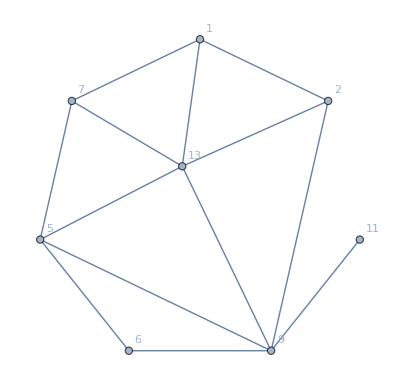
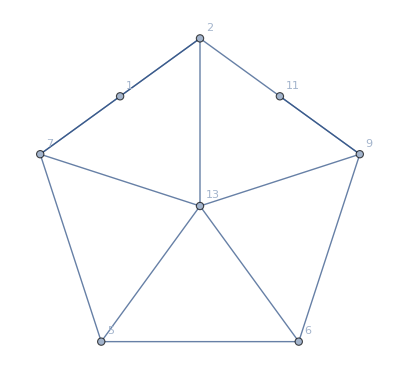
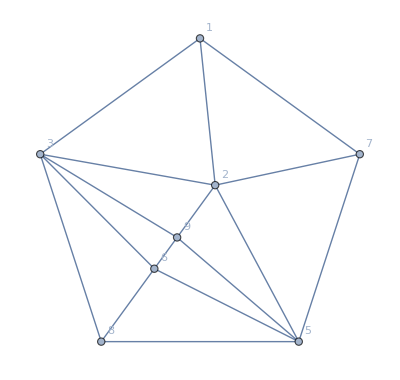
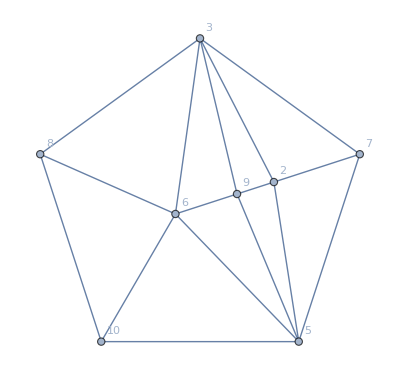
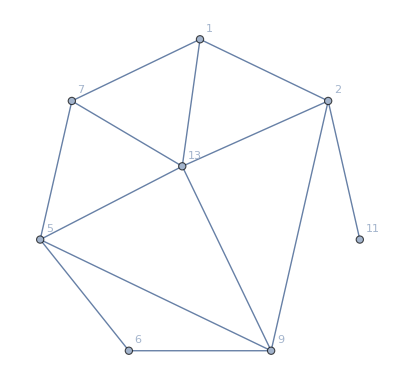
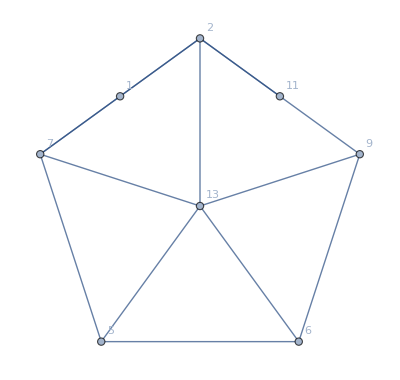
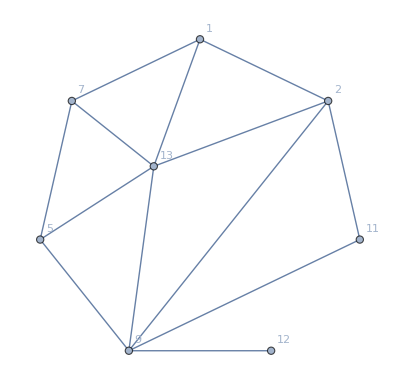
{-Graphics-{20019,{1,2,7,9,5}},-Graphics-{20020,{2,7,9,5,6}},-Graphics-{20022,{1,3,7,5,8}},-Graphics-{20024,{3,7,5,8,10}},-Graphics-{20043,{1,3,7,5,8}},-Graphics-{20044,{3,7,5,8,10}},-Graphics-{20059,{1,2,7,9,5}},-Graphics-{20060,{2,7,9,5,6}},-Graphics-{20063,{3,7,5,8,10}},-Graphics-{20078,{1,2,7,9,5}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==5&],10]]
```

```mathematica
DeleteVertices2[g_Graph,border_, center_]:=Block[{result=g,three},
result=VertexDelete[result,center];
three=Select[VertexList[result],!MemberQ[border,#]&&VertexDegree[result,#]==3&];
While[three≠{},
result=VertexDelete[result,three];
three=Select[VertexList[result],!MemberQ[border,#]&&VertexDegree[result,#]==3&];
];
Graph[result,GraphLayout->"PlanarEmbedding",GraphHighlight->border,VertexLabels->"Name"]
]
```

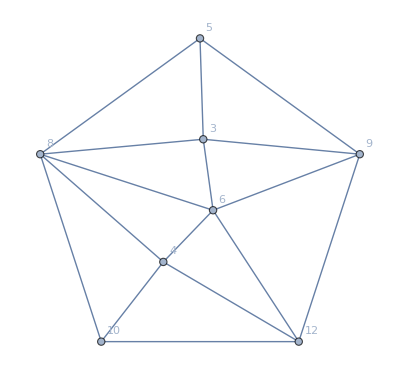
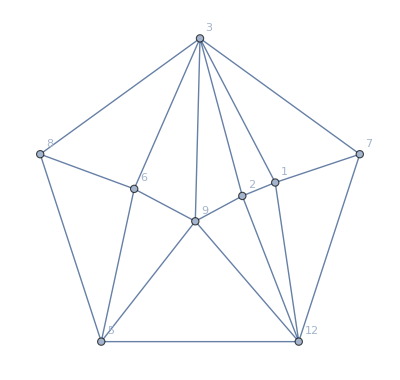
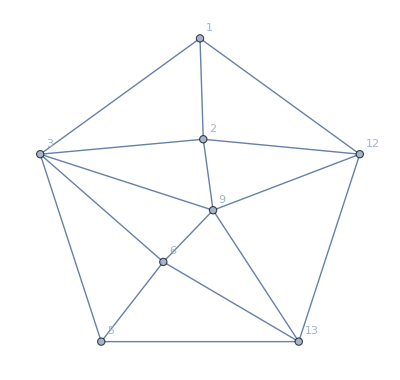
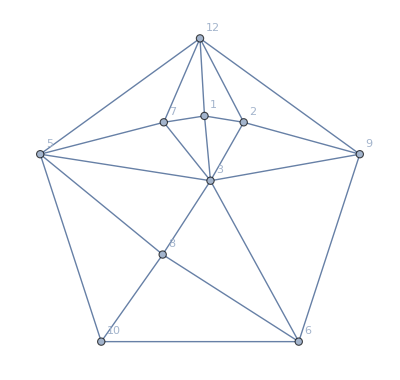
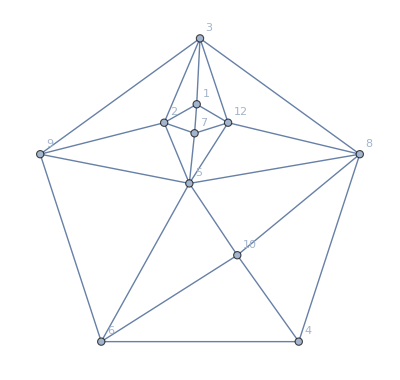
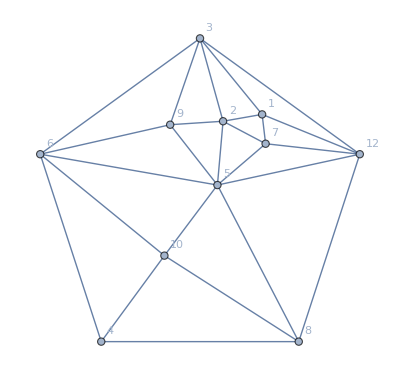
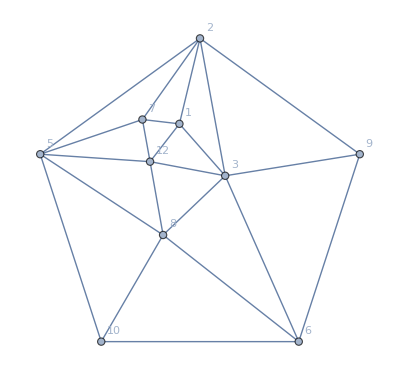
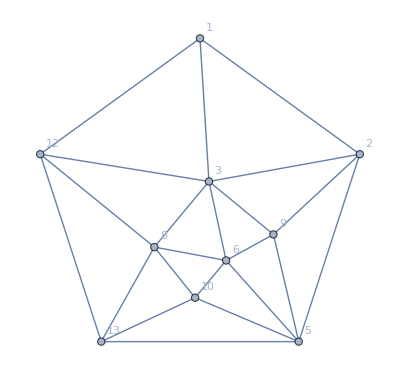
{-Graphics-{20000,{5,9,8,10,12}},-Graphics-{20209,{3,7,12,8,5}},-Graphics-{20215,{1,3,12,5,13}},-Graphics-{20216,{12,9,5,6,10}},-Graphics-{20254,{3,9,8,4,6}},-Graphics-{20255,{3,12,6,4,8}},-Graphics-{20257,{2,5,9,6,10}},-Graphics-{20260,{1,2,12,5,13}},-Graphics-{20260,{1,3,7,8,13}},-Graphics-{20260,{7,12,5,8,10}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==4&],10]]
```

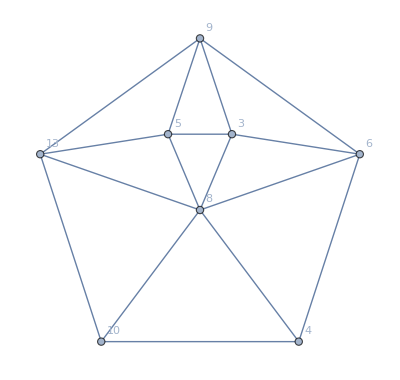
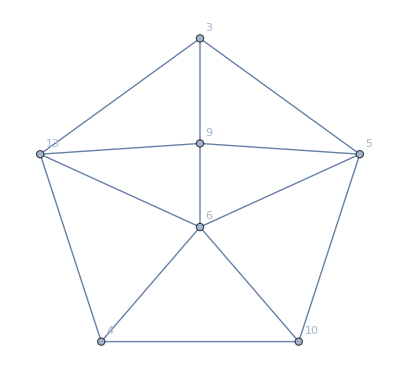
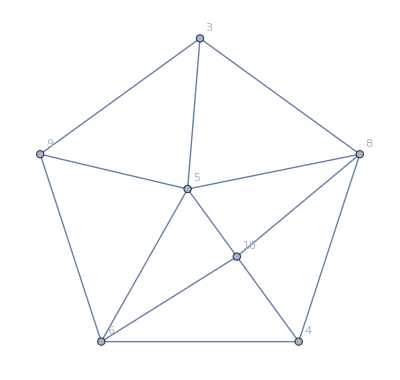
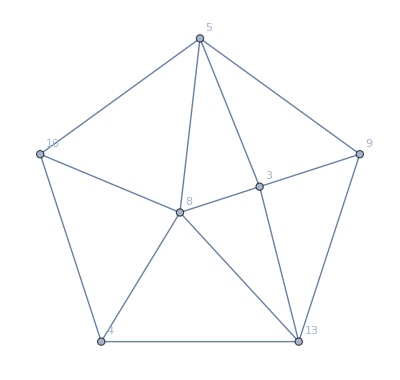
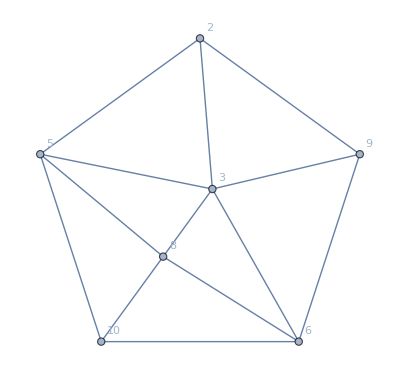
{-Graphics-{20000,{9,6,4,10,13}},-Graphics-{20029,{3,5,13,4,10}},-Graphics-{20029,{3,9,8,4,6}},-Graphics-{20029,{5,9,13,4,10}},-Graphics-{20031,{2,5,9,6,10}},-Graphics-{20049,{3,5,13,4,10}},-Graphics-{20049,{3,9,8,4,6}},-Graphics-{20049,{5,9,13,4,10}},-Graphics-{20051,{2,5,9,6,10}},-Graphics-{20068,{3,5,13,4,10}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==3&],10]]
```

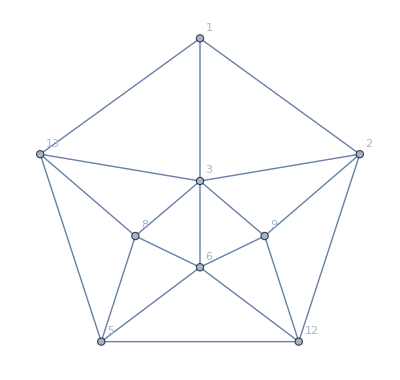
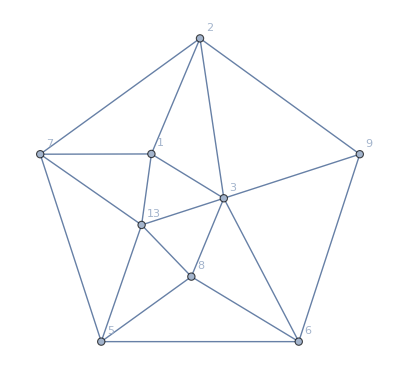
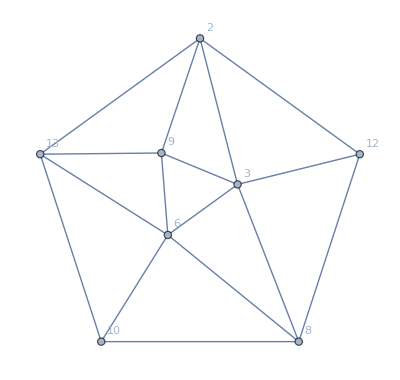
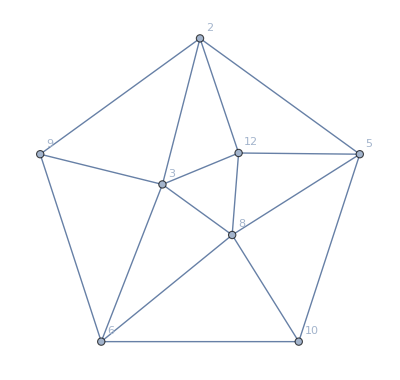
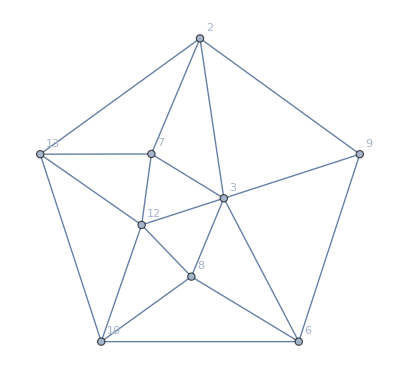
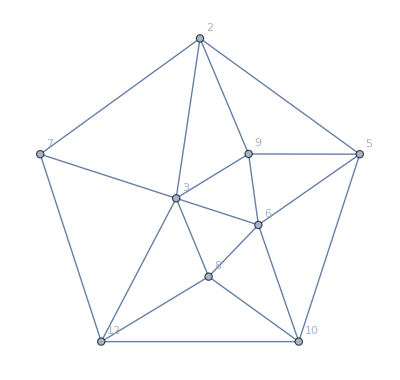
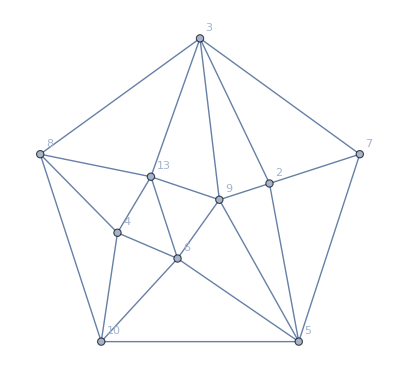
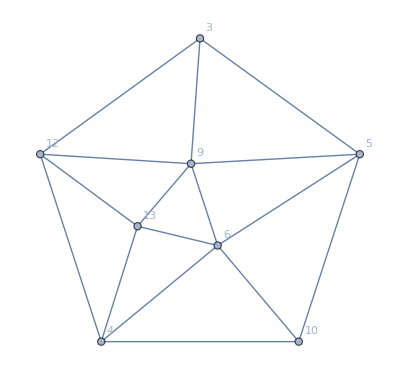
{-Graphics-{20225,{1,2,13,12,5}},-Graphics-{20225,{2,7,9,6,5}},-Graphics-{20246,{2,12,13,8,10}},-Graphics-{20246,{2,5,9,6,10}},-Graphics-{20286,{2,9,13,6,10}},-Graphics-{20286,{2,7,5,12,10}},-Graphics-{20288,{3,7,5,8,10}},-Graphics-{20319,{3,5,12,4,10}},-Graphics-{20319,{3,9,8,4,13}},-Graphics-{20319,{8,12,6,10,13}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==2&],10]]
```

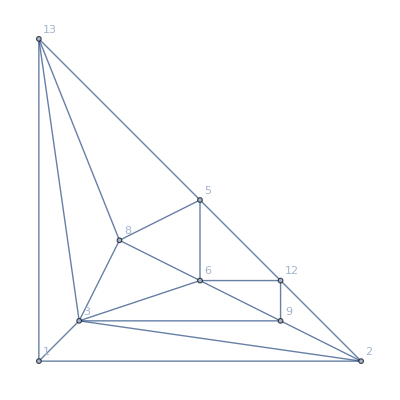
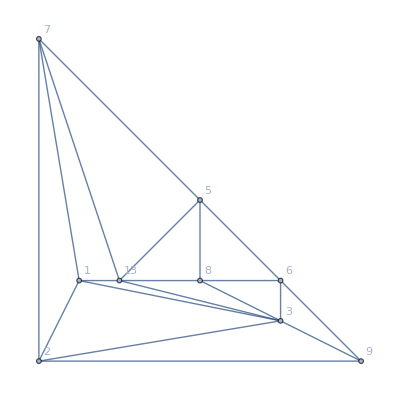
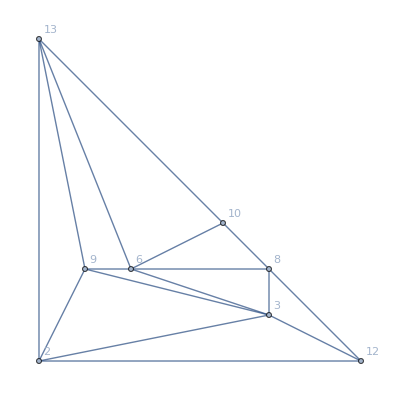
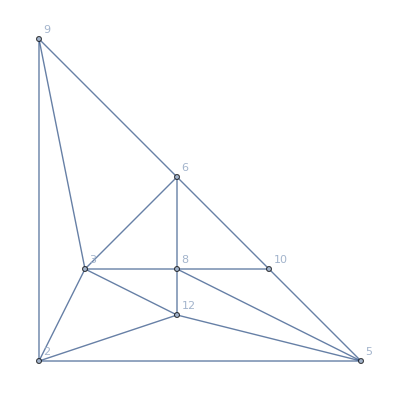
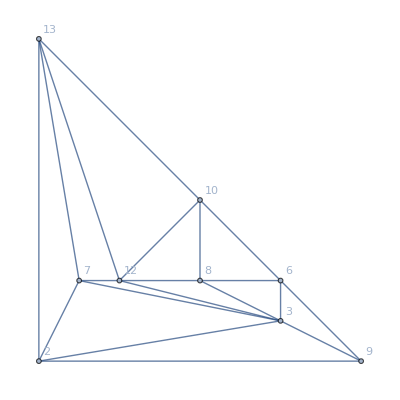
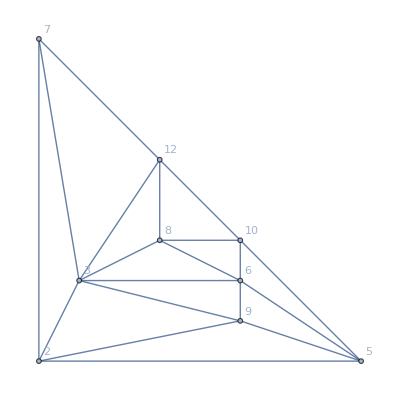
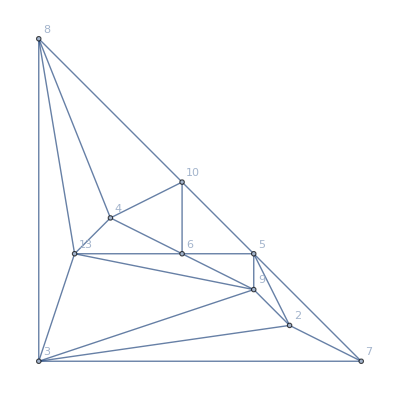
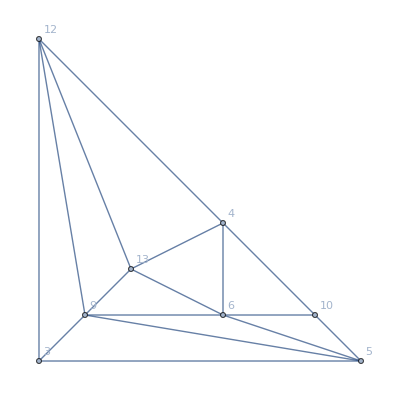
{-Graphics-{20225,{1,2,13,12,5}},-Graphics-{20225,{2,7,9,6,5}},-Graphics-{20246,{2,12,13,8,10}},-Graphics-{20246,{2,5,9,6,10}},-Graphics-{20286,{2,9,13,6,10}},-Graphics-{20286,{2,7,5,12,10}},-Graphics-{20288,{3,7,5,8,10}},-Graphics-{20319,{3,5,12,4,10}},-Graphics-{20319,{3,9,8,4,13}},-Graphics-{20319,{8,12,6,10,13}}}

```mathematica
Map[Labeled[DeleteVertices2[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==2&],10]]
```

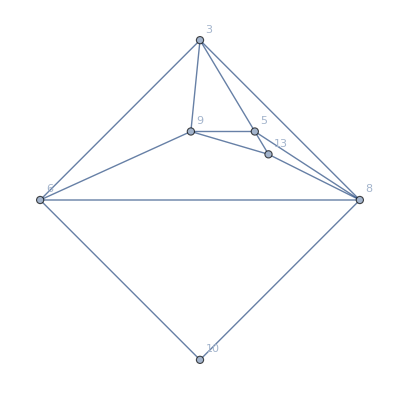
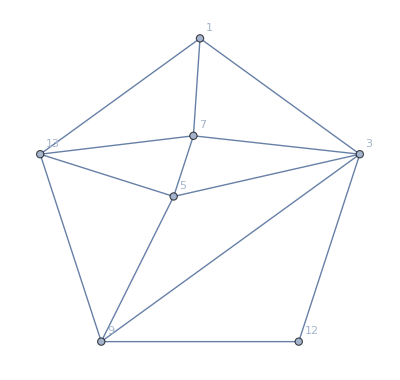
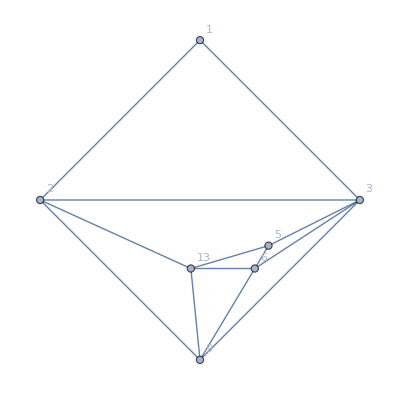
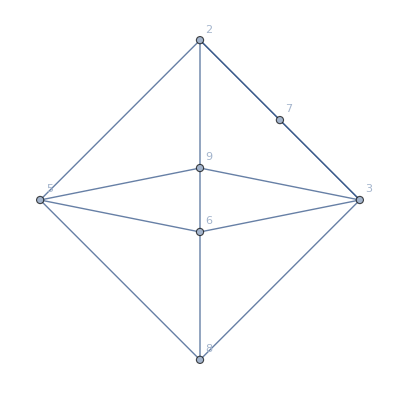
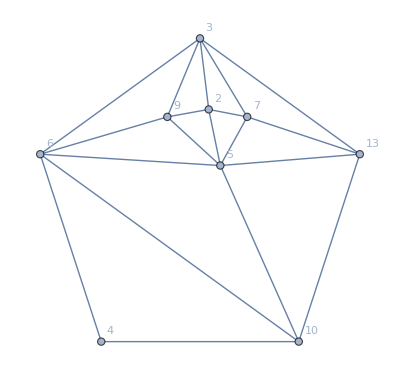
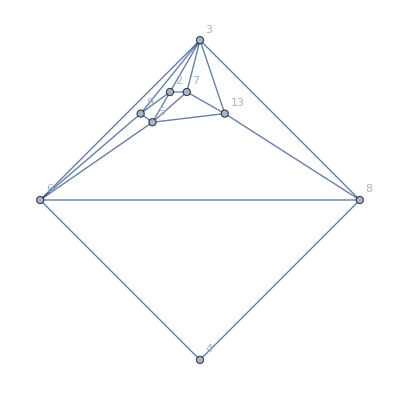
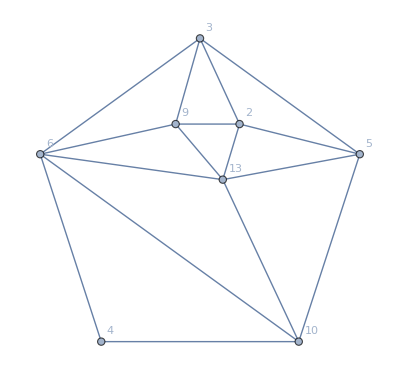
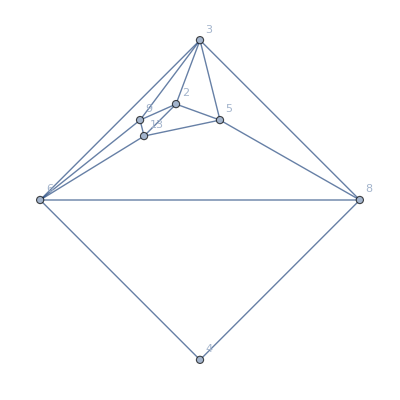
{-Graphics-{20002,{9,6,8,10,13}},-Graphics-{20019,{1,3,13,9,12}},-Graphics-{20020,{1,2,3,13,5}},-Graphics-{20021,{2,3,7,5,8}},-Graphics-{20024,{3,6,13,4,10}},-Graphics-{20024,{5,6,8,13,4}},-Graphics-{20031,{3,5,6,4,10}},-Graphics-{20031,{5,13,6,8,4}},-Graphics-{20042,{2,3,7,5,8}},-Graphics-{20044,{3,6,13,4,10}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==6&&#[[4]]==2&],10]]
```

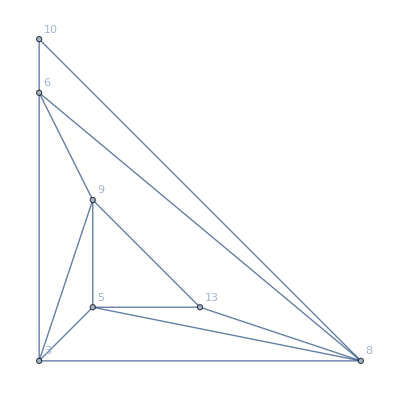
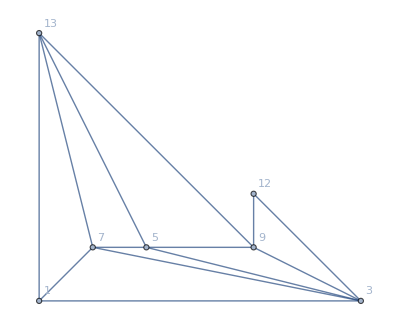
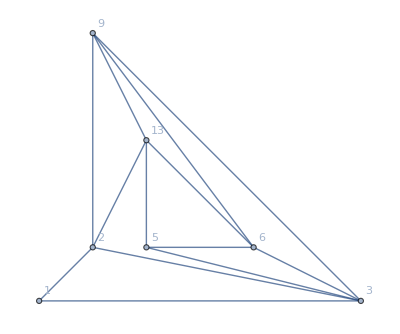
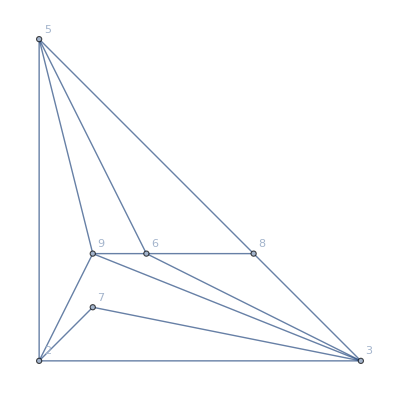
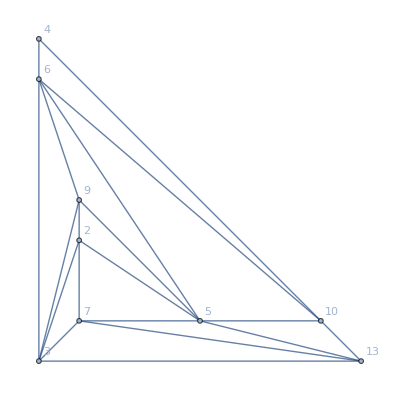
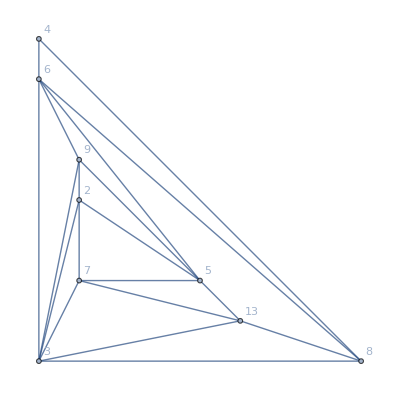
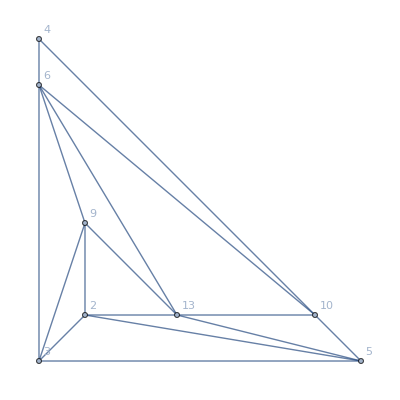
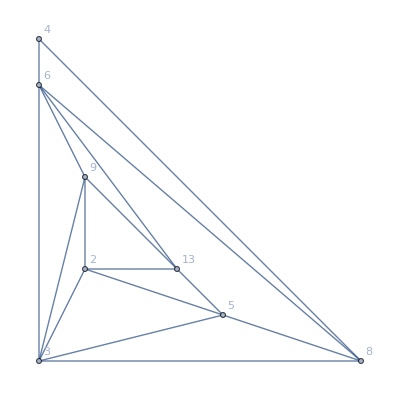
{-Graphics-{20002,{9,6,8,10,13}},-Graphics-{20019,{1,3,13,9,12}},-Graphics-{20020,{1,2,3,13,5}},-Graphics-{20021,{2,3,7,5,8}},-Graphics-{20024,{3,6,13,4,10}},-Graphics-{20024,{5,6,8,13,4}},-Graphics-{20031,{3,5,6,4,10}},-Graphics-{20031,{5,13,6,8,4}},-Graphics-{20042,{2,3,7,5,8}},-Graphics-{20044,{3,6,13,4,10}}}

```mathematica
Map[Labeled[DeleteVertices2[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==6&&#[[4]]==2&],10]]
```

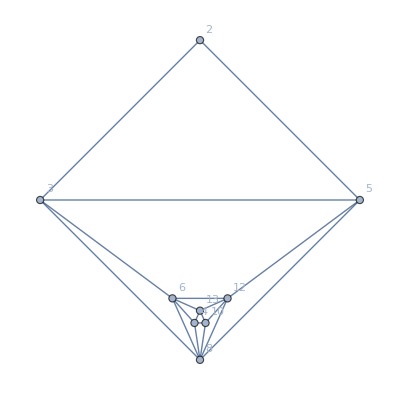
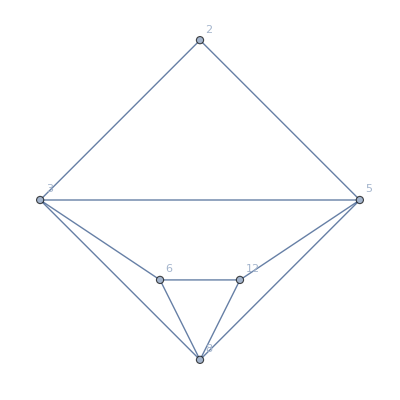
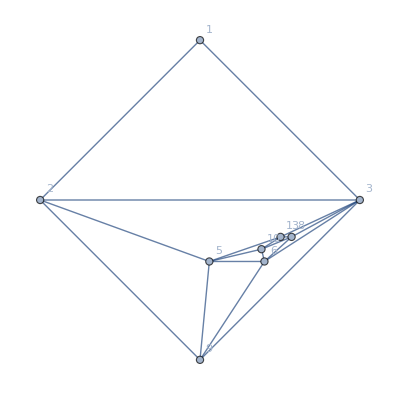
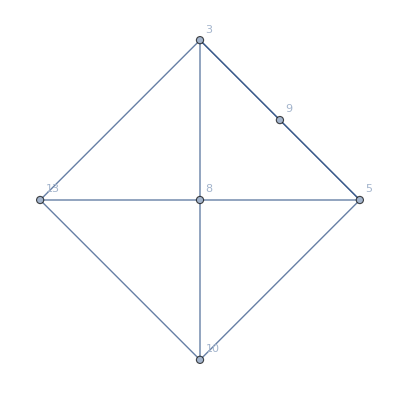
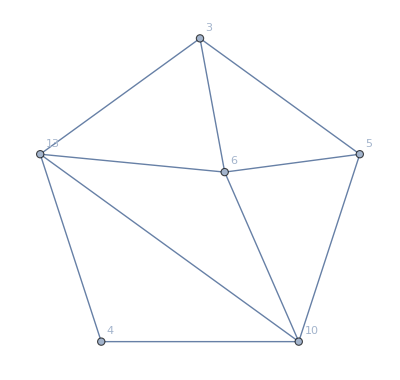
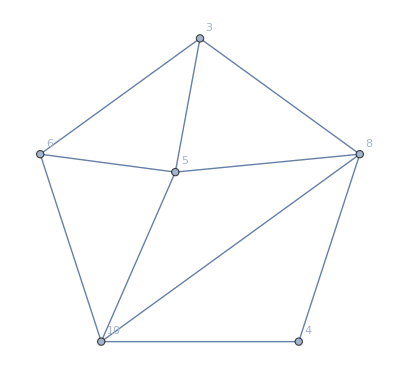
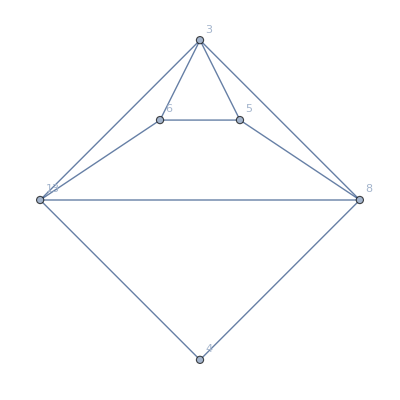
{-Graphics-{20001,{2,3,5,6,12}},-Graphics-{20003,{2,3,5,6,12}},-Graphics-{20004,{2,3,5,6,12}},-Graphics-{20005,{2,3,5,6,12}},-Graphics-{20008,{2,3,5,6,12}},-Graphics-{20024,{1,2,3,5,13}},-Graphics-{20028,{3,5,9,13,10}},-Graphics-{20028,{3,5,13,4,10}},-Graphics-{20028,{3,6,8,4,10}},-Graphics-{20028,{5,6,8,13,4}}}

```mathematica
Map[Labeled[DeleteVertices[Graph[EdgeList[ReadGrof[#[[1]]]],GraphLayout->"CircularEmbedding"],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==6&&#[[4]]==3&],10]]
```

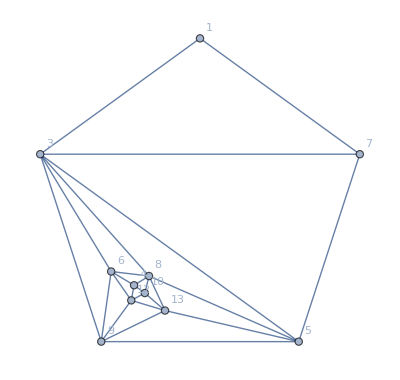
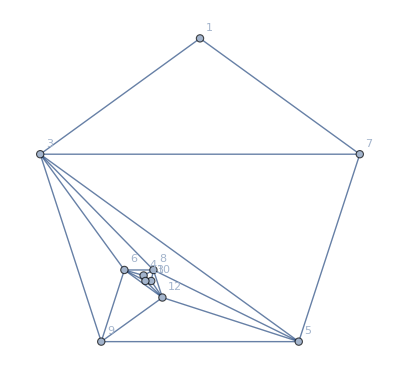
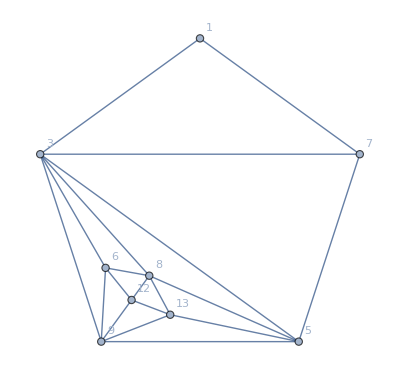
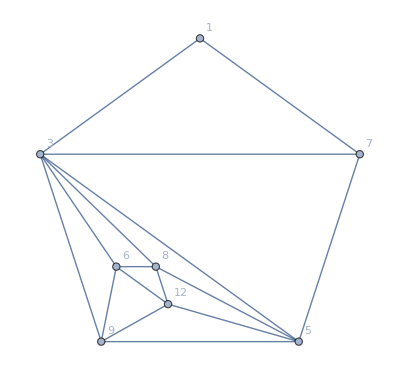
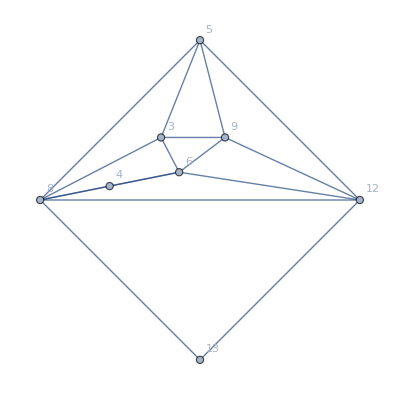
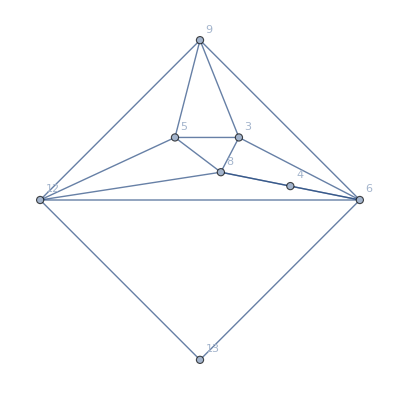
{-Graphics-{20000,{1,3,7,5,9}},-Graphics-{20001,{1,3,7,5,9}},-Graphics-{20002,{1,3,7,5,9}},-Graphics-{20003,{1,3,7,5,9}},-Graphics-{20004,{1,3,7,5,9}},-Graphics-{20004,{6,8,4,12,13}},-Graphics-{20005,{1,3,7,5,9}},-Graphics-{20005,{6,8,4,12,13}},-Graphics-{20006,{1,3,7,5,9}},-Graphics-{20007,{1,3,7,5,9}}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]],FindCenter[#[[1]],#[[2,1,1]]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==7&&#[[4]]==1&],10]]
```